## Part I quantum mechanics in one dimension

```mathematica
$Assumptions=L>0&&w>0&&w>0&&t>0&&m>0&&h>0;
```

#### basic wave mechanics

Hamiltonian as an operator acting on the wavefunction

```mathematica
ha[V_]@psi_:=-h^2/(2m) D[psi,{x,2}]+V psi
```

example

```mathematica
ha[vo]@(E^(I k x))//Collect[#,E^(I k x)]&
```

ⅇ^(ⅈ k x) ((h^2 k^2)/(2 m)+vo)

linearity

```mathematica
ha[V]@(a f[x]+b g[x])==a ha[V]@f[x]+b ha[V]@g[x]//ExpandAll
```

True

EOM

```mathematica
p@psi_:=-I h D[psi,x]
```

```mathematica
1/(2m)p@p@psi[x]
```

-(h^2 psi''[x])/(2 m)

```mathematica
ha[0]@psi[x]==%
```

True

define the Schrodinger equation

```mathematica
sD[V_]@psi_:=ha[V]@psi-Energy psi
```

```mathematica
sD[V[x]]@psi[x]==0
```

-Energy psi[x]+psi[x] V[x]-(h^2 psi''[x])/(2 m)==0

principle of superposition is nothing but the fact that wave/Schrodinger equation is a linear differential equation.

#### particle in a box

analytical eigenfunctions

```mathematica
phi[n_,x_]:=norm[n]Sin[n π x/L]
```

```mathematica
sD[0]@phi[n,x]/phi[n,x]==0//ExpandAll
```

-Energy+(h^2 n^2 π^2)/(2 L^2 m)==0

```mathematica
e[n_]=Energy/.Solve[%,Energy][[1]]
```

(h^2 n^2 π^2)/(2 L^2 m)

⇒ n is a positive integer

```mathematica
norm[n_]=norm[n]/.Solve[
Integrate[phi[n,x]^2,{x,0,L}]==1/.Sin[m_Integer n π]->0,norm[n]
][[1]]
```

-(√2)/(√L)

```mathematica
Integrate[phi[n,x]^2,{x,0,L}]
```

1-Sin[2 n π]/(2 n π)

numerical eigenfunctions

```mathematica
sD[0]@phi[x]==0/.{h->1,m->1}
```

-Energy phi[x]-phi''[x]/2==0

shooting method

```mathematica
Manipulate[
Plot[
Evaluate[phi[x]/.(NDSolve[
{sD[0]@phi[x]==0,phi[0]==0,phi'[0]==1}/.{h->1,m->1,Energy->sol},
phi,{x,0,1.1}
])],{x,0,1.1},
PlotRange->{-0.5,0.5},
Epilog->{{Line[{{1,-2},{1,2}}]}}
],{sol,2,6}]
```

basic properties

```mathematica
Integrate[phi[m,x]phi[n,x],{x,0,L}]
```

(2 n Cos[n π] Sin[m π]-2 m Cos[m π] Sin[n π])/(m^2 π-n^2 π)

```mathematica
c[n_]=Integrate[√(2/L)phi[n,x],{x,L/4,3L/4}]
```

-(4 Sin[(n π)/4] Sin[(n π)/2])/(n π)

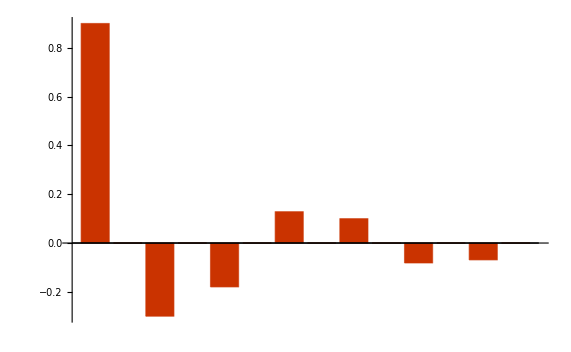

```mathematica
Block[{L=1},BarChart[-Table[c[n],{n,1,14}],PlotRange->All]]
```

Gibbs phenomenon (“Gibbs horns”, reduced by Lanczos sigma-factors)

```mathematica
Manipulate[Plot[Evaluate[Abs@Sum[c[i]phi[i,x],{i,1,n}]/.L->1//N],{x,0,1},
Epilog->{Dashing[{.01,.01}],
Line[{{.25,0},{.25,√2}}],
Line[{{.75,0},{.75,√2}}],
Line[{{.25,√2},{.75,√2}}]},PlotRange->{All,{0,2}}],{n,1,80,1}]
```

#### quantum rattle

```mathematica
a[n_]:=1/√2
a[n_,t_]:=a[n]E^(-I e[n]t/h)
psi[x_,t_]:=Sum[a[n,t]phi[n,x],{n,2}]
```

```mathematica
I h D[psi[x,t],t]==ha[0]@psi[x,t]//ExpandAll
```

True

```mathematica
psi[0,t]==psi[L,t]==0
```

True

```mathematica
psisq[x_,t_]=psi[x,t]*psi[x,t]//Expand//ComplexExpand//FullSimplify
```

((3+2 Cos[(2 π x)/L]+2 Cos[(π (3 h π t-2 L m x))/(2 L^2 m)]+2 Cos[(π (3 h π t+2 L m x))/(2 L^2 m)]) Sin[(π x)/L]^2)/L

```mathematica
Integrate[psisq[x,t],{x,0,L}]
```

1

```mathematica
Integrate[psisq[x,t],{x,0,L/2}]
```

1/2+(4 Cos[(3 h π^2 t)/(2 L^2 m)])/(3 π)

```mathematica
Manipulate[Plot[Evaluate[psisq[x,t]/.{h->1,L->1,m->1}//N],{x,0,1}],{t,0,.8}]
```

```mathematica
xExp[t_]=Integrate[x psisq[x,t],{x,0,L}]
```

1/18 L (9-(32 Cos[(3 h π^2 t)/(2 L^2 m)])/π^2)

```mathematica
xsqExp[t_]=Integrate[x^2psisq[x,t],{x,0,L}]
```

(L^2 (-45+48 π^2-256 Cos[(3 h π^2 t)/(2 L^2 m)]))/(144 π^2)

```mathematica
p@psi_:=-I h D[psi,x]
pExp[t_]=
Integrate[psi[x,t]*p@psi[x,t],{x,0,L}]//Expand//ComplexExpand//FullSimplify
```

(8 h Sin[(3 h π^2 t)/(2 L^2 m)])/(3 L)

```mathematica
D[xExp[t],t]==pExp[t]/m
```

True

```mathematica
psqExp[t_]=
Integrate[ComplexExpand[psi[x,t]*]p@p@psi[x,t],{x,0,L}]//Expand
```

(5 h^2 π^2)/(2 L^2)

```mathematica
psqExp[t]/2/m==(e[1]+e[2])/2
```

True

#### uncertainty principle

```mathematica
psiPW[n_]:=Sum[E^(I k x),{k,2.4,2.6,(2.6-2.4)/(n-1)}]/n
Manipulate[Plot[Abs[psiPW[n]^2],{x,-150,150},PlotRange->{All,{0,1}}],{n,2,10,1}]
```

```mathematica
2π/.2
```

31.4159

#### free-particle wave packet

```mathematica
phi[k_]=(π w)^(-1/4)E^(-k^2/2/w)
```

(ⅇ^(-k^2/(2 w)))/(π^(1/4) w^(1/4))

```mathematica
Integrate[phi[k]^2,{k,-Infinity,Infinity}]
```

1

```mathematica
psi[x_]=1/√(2π)*Integrate[phi[k] E^(I k x),{k,-Infinity,Infinity}]
```

(ⅇ^(-(w x^2)/2) w^(1/4))/π^(1/4)

```mathematica
Integrate[psi[x]^2,{x,-Infinity,Infinity}]
```

1

moving wavepacket

```mathematica
psi[x_,0]=1/√(2π)*Integrate[phi[k-kp] E^(I k x),{k,-Infinity,Infinity}]/.E^m_:>E^(Expand@m)
```

(ⅇ^(ⅈ kp x-(w x^2)/2) w^(1/4))/π^(1/4)

```mathematica
phi[k_,t_]:=phi[k-kp] E^(-I h k^2/2/m t)
psi[x_,t_]=Integrate[phi[k,t]E^(I k x)/√(2π),{k,-Infinity,Infinity}]//ExpandAll//MapAll[Together,#]&
```

(ⅇ^(-(h kp^2 t)/(2 (-ⅈ m+h t w))+(kp m x)/(-ⅈ m+h t w)+(ⅈ m w x^2)/(2 (-ⅈ m+h t w))))/(π^(1/4) w^(1/4) √((m+ⅈ h t w)/(m w)))

```mathematica
Quiet@ListPointPlot3D[Flatten[Table[{x,t,Chop@Evaluate[psi[x,t]*psi[x,t]/.{h->1,m->1,w->1,kp->2}//N]},{x,-5,30,.1},{t,0,11,1}],1],PlotRange->All]
```

-Graphics3D-

group velocity h kp/m differs from phase velocity h k/(2m), happens as long as the frequency is not simply proportional to wavenumber, e.g., classical waves in a dispersive medium. Here e[k]/h is proportional to k^2.

#### parity

```mathematica
vEven[a_.x_?Negative]:=vEven[-a x]
```

```mathematica
vEven[-x]==vEven[x]
```

True

```mathematica
parity@psi_:=psi/.{x->-x,y->-y,z->-z}//ExpandAll
```

```mathematica
{parity@psii[x],parity@vEven[x],parity@x^2}
```

{psii[-x],vEven[x],x^2}

#### harmonic oscillator

```mathematica
(* RuleDelayed: evaluating rhs only after the rule is used *)
Series[V[x],{x,x0,2}]/.{V[x0]:>V0,V'[x0]:>0,V''[x0]:>k}
```

V0+1/2 k (x-x0)^2+O[x-x0]^3

```mathematica
VHO=%/.{x0->0,V0->0,k->m w^2}//Normal
```

1/2 m w^2 x^2

```mathematica
Clear[psi]
sD[V_]@psi:=-h^2/2/m D[psi,{x,2}]+V psi- Energy psi
sD[VHO]@psi[x]==0
```

-Energy psi[x]+1/2 m w^2 x^2 psi[x]-(h^2 psi''[x])/(2 m)==0

scale the Schrodinger equation

```mathematica
(* firstly set the length scale by a *)
-2m/(a h)^2 sD[VHO]@psi[a x]==0//ExpandAll
```

(2 Energy m psi[a x])/(a^2 h^2)-(m^2 w^2 x^2 psi[a x])/(a^2 h^2)+psi''[a x]==0

```mathematica
(* simplify the second term on the lhs of above equation *)
%/.x->z/a/.a->√(m w/h)
```

(2 Energy psi[z])/(h w)-z^2 psi[z]+psi''[z]==0

```mathematica
(%/.Energy->h w(n+1/2)//Expand//Collect[#,psi[z]]&)==0
```

((1+2 n-z^2) psi[z]+psi''[z]==0)==0

solve this differential equation by power series, particularly useful when the coefficients are polynomials.

```mathematica
hermiteDt[H_]=
(Dt[psi,{z,2}]+(1+2n-z^2)psi)E^(z^2/2)/.psi->E^(-z^2/2)H//Expand
```

2 H n-2 z Dt[H,z]+Dt[H,{z,2}]

```mathematica
SetAttributes[{c,k},Constant]
```

```mathematica
hermiteDt[H]/.H->c[n,k]z^k//ExpandAll
```

-k z^(-2+k) c[n,k]+k^2 z^(-2+k) c[n,k]-2 k z^k c[n,k]+2 n z^k c[n,k]

```mathematica
%/.{k^(m_.)c[n,k] z^(k+q_.)->(k-q)^m c[n,k-q],
c[n,k] z^(k+q_.)->c[n,k-q]}//Collect[#,{c[n,k],c[n,k+2]}]&//Map[Factor,#]&
```

-2 (k-n) c[n,k]+(1+k) (2+k) c[n,2+k]

```mathematica
(* a neat usage of generating replecement rule! *)
cRep=Solve[%==0,c[n,k+2]][[1,1]]/.k->k-2//ExpandAll//MapAll[Factor,#]&
```

c[n,k]→(2 (-2+k-n) c[n,-2+k])/((-1+k) k)

dynamical-programming functions!

```mathematica
cEven[n_,0]:=1
cEven[n_,1]:=0
(* Evaluateensures that the replacement with cRep is made even though SetDelayed(:=)is needed for the dynamic program *)
cEven[n_,k_]:=c[n,k]/.cRep/.c->cEven//Evaluate
```

```mathematica
cOdd[n_,1]:=1
cOdd[n_,0]:=0
cOdd[n_,k_]:=c[n,k]/.cRep/.c->cOdd//Evaluate
```

```mathematica
?cEven
```

```mathematica
?cOdd
```

```mathematica
Sum[cEven[n,k]z^k,{k,0,7}]
```

1-n z^2-1/6 (2-n) n z^4-1/90 (2-n) (4-n) n z^6

```mathematica
Sum[cOdd[n,k]z^k,{k,0,7}]
```

z+1/3 (1-n) z^3+1/30 (1-n) (3-n) z^5+1/630 (1-n) (3-n) (5-n) z^7

```mathematica
H[n_,z_]:=If[EvenQ[n],
2^n/cEven[n,n]Sum[cEven[n,k]z^k,{k,0,n}]//Expand,
2^n/cOdd[n,n]Sum[cOdd[n,k]z^k,{k,0,n}]//Expand
]
```

```mathematica
{H[0,z],H[1,z],H[2,z],H[3,z]}
```

{1,2 z,-2+4 z^2,-12 z+8 z^3}

```mathematica
%==Table[HermiteH[i,z],{i,0,3,1}]
```

True

Hermite polynomials are orthogonal functions appeared in eigenvalue problems of Hermitian 2ed-order differential operators known as Sturm-Liouville theory.

orthogonal w.r.t. their weight function

```mathematica
Block[{m=2,n=10},Integrate[E^(-z^2)HermiteH[m,z]HermiteH[n,z],{z,-Infinity,Infinity}]==0]
```

True

normalizable

```mathematica
Block[{n=7},Integrate[E^(-z^2)H[n,z]^2,{z,-Infinity,Infinity}]==2^n n!√π]
```

True

Hypergeometric functions

confluent hypergeometric or Kummer’s differential equation:

```mathematica
kummerDt[f_]=z Dt[f,{z,2}]+(b-z)Dt[f,z]-a f;
```

```mathematica
kummerDt[f[z]]==0
```

-a f[z]+(b-z) f'[z]+z f''[z]==0

Hypergeometric functions unify most of the common solutions which arise from separation of variables of Laplace’s equation, the diffusion equation, the classical wave equation, and the Schrodinger equation, etc.

```mathematica
Hypergeometric1F1[a,b,z]+O[z]^4 (* normalized in the sense that they all equal unity at z=0 *)
```

1+(a z)/b+(a (1+a) z^2)/(2 b (1+b))+(a (1+a) (2+a) z^3)/(6 b (1+b) (2+b))+O[z]^4

```mathematica
hermiteDt[f[z^2]]/4==0/.n->2n/.z->√y//ExpandAll//Collect[#,{f[y],f'[y]}]&
```

n f[y]+(1/2-y) f'[y]+y f''[y]==0

```mathematica
hermiteDt[f[z^2]]/4==0/.n->2n+1/.z->√y//ExpandAll//Collect[#,{f[y],f'[y]}]&
```

(1/2+n) f[y]+(1/2-y) f'[y]+y f''[y]==0

```mathematica
SetAttributes[{nu},Constant]
```

```mathematica
kummerDt[z^nu f[z]]/z^nu==0//ExpandAll//Collect[#,{f[z],f'[z]}]&
```

(-a-nu-nu/z+(b nu)/z+nu^2/z) f[z]+(b+2 nu-z) f'[z]+z f''[z]==0

```mathematica
%/.nu->1-b//ExpandAll//Collect[#,{f[z],f'[z]}]&
```

(-1-a+b) f[z]+(2-b-z) f'[z]+z f''[z]==0

```mathematica
HypergeometricU[a,b,z]+O[z]^4
```

HypergeometricU[a,b,z]+O[z]^4

```mathematica
Series[HypergeometricU[a,b,z],{z,0,3}]
```

z^-b ((Gamma[-1+b] z)/Gamma[a]+((-1-a+b) Gamma[-1+b] z^2)/((-2+b) Gamma[a])+((-2-a+b) (-1-a+b) Gamma[-1+b] z^3)/(2 (-3+b) (-2+b) Gamma[a])+O[z]^4)+(Gamma[1-b]/Gamma[1+a-b]+(a Gamma[1-b] z)/(b Gamma[1+a-b])+(a (1+a) Gamma[1-b] z^2)/(2 b (1+b) Gamma[1+a-b])+(a (1+a) (2+a) Gamma[1-b] z^3)/(6 b (1+b) (2+b) Gamma[1+a-b])+O[z]^4)

```mathematica
Hypergeometric2F1[a,b,c,z]+O[z]^3
```

1+(a b z)/c+(a (1+a) b (1+b) z^2)/(2 c (1+c))+O[z]^3

```mathematica
?HypergeometricPFQ
```

```mathematica
?Pochhammer
```

normalized HO wavefunctions

```mathematica
(* dynamic-programming f[x_]:=f[x]=expr to save result as it's calculated, i.e., retrieve results from computer memory rather than recompute *)
psiHOz[n_,z_]:=psiHOz[n,z]=znorm[n] E^(-z^2/2)HermiteH[n,z]
```

```mathematica
(* MMA cannot deal with this integral! *)
Integrate[psiHOz[n,z]^2,{z,-Infinity,Infinity}]
```

Integrate::idiv: Integral of ⅇ^(-z^2) HermiteH[n,z]^2 znorm[n]^2 does not converge on {-∞,∞}.

∫_(-∞)^∞ ⅇ^(-z^2) HermiteH[n,z]^2 znorm[n]^2ⅆz

```mathematica
(* we then do it manually *)
psiHOz[n,z]^2==1/.f_. E^(-z^2)HermiteH[n,z]^2->f 2^n n!√π
```

2^n √π n! znorm[n]^2==1

```mathematica
znorm[n_]=znorm[n]/.Solve[%,znorm[n]][[1]]
```

-2^(-n/2)/(π^(1/4) √(n!))

```mathematica
(* convert back to the physical variable *)
psiHO[n_,x_]:=psiHO[n,x]=(m w/h)^(1/4)psiHOz[n,z]/.z->√(m w/h)x
```

```mathematica
eHO[n_]=h w (n+1/2);
ha[VHO]@psiHO[2,x]==eHO[2]psiHO[2,x]//ExpandAll//FullSimplify
```

True

```mathematica
Table[Integrate[psiHO[i,x]^2,{x,-Infinity,Infinity}],{i,3}]
```

{1,1,1}

```mathematica
Integrate[psiHO[0,x]psiHO[2,x],{x,-Infinity,Infinity}]
```

0

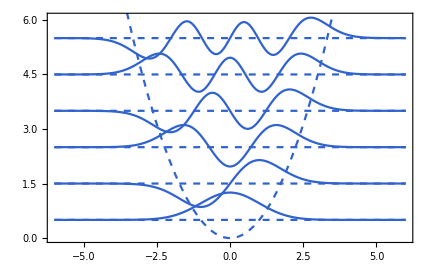

```mathematica
Show[Plot[Table[Evaluate[(1/2+i)-psiHO[i,x]/.{h->1,w->1,m->1}//N],{i,0,5}],{x,-6,6}],Plot[Table[Evaluate[(1/2+i)],{i,0,5}],{x,-6,6},PlotStyle->Dashed],
Plot[Evaluate[VHO/.{h->1,w->1,m->1}//N],{x,-6,6},PlotStyle->Dashed]]
```

raising and lowering operators

```mathematica
p@psi_:=-I h D[psi,x]
aR@psi_:=√(m w/2/h)(x psi-I p@psi/m/w)
aL@psi_:=√(m w/2/h)(x psi+I p@psi/m/w)
```

```mathematica
aR@psiHO[0,x]==psiHO[1,x]//FullSimplify
```

True

```mathematica
aL@psiHO[1,x]==psiHO[0,x]//FullSimplify
```

True

```mathematica
aL@psiHO[0,x]==0
```

True

```mathematica
ha[VHO]@psi[x]==h w aL@aR@psi[x]-h w/2psi[x]==h w aR@aL@psi[x]+h w/2psi[x]//FullSimplify
```

True

#### variational method and perturbation ideas

if the trial function is orthogonal to the true ground state wave function (obtained, say, by symmetry), then the trial energy will give a least upper bound on the first excited state.

```mathematica
psi[0,a_,x_]:=√a π^(-1/4)E^(-a^2 x^2/2)
```

```mathematica
xsq[0]=Integrate[x^2 psi[0,a,x]^2,{x,-Infinity,Infinity},Assumptions->a>0]
```

1/(2 a^2)

```mathematica
p@psi_:=-I h D[psi,x]
psq[0]=Integrate[psi[0,a,x]p@p@psi[0,a,x],{x,-Infinity,Infinity},Assumptions->a>0]
```

(a^2 h^2)/2

```mathematica
eTrial[0]=psq[0]/2/m+m w^2/2xsq[0]
```

(a^2 h^2)/(4 m)+(m w^2)/(4 a^2)

```mathematica
Solve[D[eTrial[0],a]==0,a][[1,1]]
```

a→-(√m √w)/(√h)

```mathematica
eTrial[0]/.%
```

(h w)/2

First excited trial states should be orthogonal to the GS. Here it is automatically satisfied if it is odd; the simplest guess is just multiplying the GS by x

```mathematica
psi[1,a_,x_]:=√(2a)π^(-1/4)a x E^(-a^2 x^2/2)
```

```mathematica
?psi
```

```mathematica
eTrial[1]=Integrate[psi[1,a,x](p@p@psi[1,a,x]/2/m+m(w x)^2/2 psi[1,a,x]),{x,-Infinity,Infinity},Assumptions->a>0]
```

(3 (a^4 h^2+m^2 w^2))/(4 a^2 m)

```mathematica
Solve[D[eTrial[1],a]==0,a][[1,1]]
```

a→-(√m √w)/(√h)

```mathematica
eTrial[1]/.%
```

(3 h w)/2

model Hamiltonian

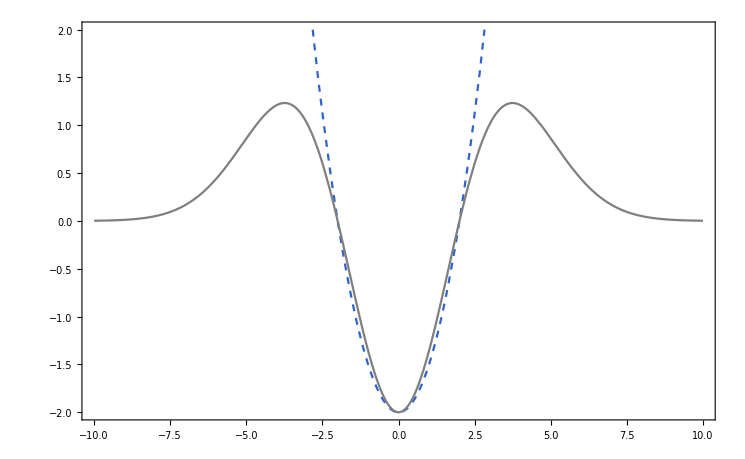

```mathematica
ha[V_]@psi_:=-1/2D[psi,{z,2}]+V psi
V=VHO E^(-b z^2);b=.1;
VHO=Vo+z^2/2;Vo=-2.0;
Plot[{VHO,V},{z,-10,10},PlotRange->{-2,2},PlotStyle->{{Dashed},{Gray}}]
```

The finite barriers can be adjusted by well minimum Vo and barrier-width parameter b. Classically for energy below the barriers, the potential supports bound orbits. Quantum mechanically, only those with negative energy is true bound states.

Energy below the barriers but positive tunnel out of the well quantum mechanically and move without bound.

In summary, negative-energy spectrum is discrete while positive-energy spectrum is continuous. Also the number of bound states is finite, unlike the HO.

The model potential is very close to the HO potential for negative energy, so the bound states must be close to those of the HO.

```mathematica
eTrial[0]=Integrate[psi[0,a,z]ha[V]@psi[0,a,z],{z,-Infinity,Infinity},Assumptions->a>0]
```

a (0.25 a+(0.05-2. a^2)/((0.1+1. a^2)^(3/2)))

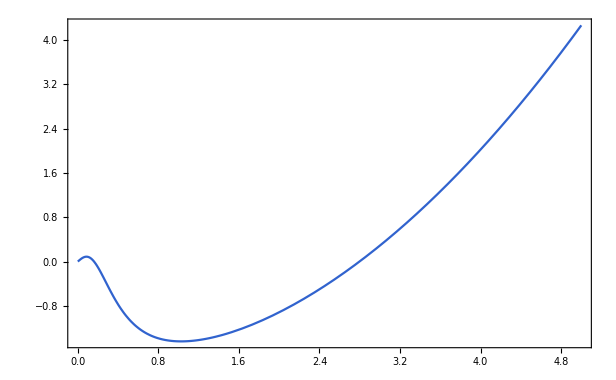

```mathematica
Plot[eTrial[0],{a,0,5}]
```

```mathematica
FindMinimum[eTrial[0],{a,1}]
```

{-1.44084,{a→1.02603}}

1st-order perturbation energy

```mathematica
VP=V-VHO;
```

```mathematica
VPExp[0]=Integrate[VP psiHOz[0,z]^2,{z,-Infinity,Infinity},Assumptions->a>0]
```

0.0597709

```mathematica
-3/2+%
```

-1.44023

Note although VP diverges as -VHO for large z with any fixed b, we only require it is small over the range of the wavefunction whose energy is being estimated, since this is what contributes to the expectation value VPExp[0].

#### squeezed states

```mathematica
psiHOw[n_,x_]:=psiHO[n,x]/.h->1
```

```mathematica
(* initial gaussian wavepacket with momentum kPo(by giving a momentum boost), displaced x=xPo, and a width different from oscillator's fundamental frequency *)
psi[x_,0]=E^(I kPo x)psiHOw[0,x-xPo]/.w->wPo
```

-(ⅇ^(ⅈ kPo x-1/2 m wPo (x-xPo)^2) (m wPo)^(1/4))/π^(1/4)

If wPo>w, the initial wave packet is narrower than HO’s GS, called the squeezed states, otherwise, also called squeezed anyway (even though it is anti-squeezed). When they equal, it is called a coherent state.

```mathematica
(* RuleDelayed is required to evaluate Map after the exponent is substituted for q*)
cintegrand=psi[x,0]psiHOw[n,x]/.E^q_:>E^Map[Factor,Collect[q,x]]
```

(2^(-n/2) ⅇ^(-1/2 m (w+wPo) x^2-1/2 m wPo xPo^2+x (ⅈ kPo+m wPo xPo)) (m w)^(1/4) (m wPo)^(1/4) HermiteH[n,√(m w) x])/(√π √(n!))

```mathematica
integrateRule=E^(c_+b_(x-y_)^2)HermiteH[n,a_ x]:>E^c √(π/(-b))(√(1+a^2/b))^n*HermiteH[n,a y/√Together[1+a^2/b]]
```

ⅇ^(c_+b_ (x-y_)^2) HermiteH[n,x a_]:>ⅇ^c √(-π/b) (√(1+a^2/b))^n HermiteH[n,(a y)/(√Together[1+a^2/b])]

```mathematica
completeSquare[e_,x_]:=e/.a_.x^2+b_.x+c_.:>a(x+b/2/a)^2+Together[b^2/(-4a)+c]
```

```mathematica
Clear[b];
E^(b x -a x^2)//completeSquare[#,x]&
```

ⅇ^(b^2/(4 a)-a (-b/(2 a)+x)^2)

```mathematica
%-E^(b x -a x^2)//ExpandAll
```

0

```mathematica
cintegrand//completeSquare[#,x]&
```

(2^(-n/2) ⅇ^((-kPo^2+2 ⅈ kPo m wPo xPo-m^2 w wPo xPo^2)/(2 m (w+wPo))-1/2 m (w+wPo) (x-(ⅈ kPo+m wPo xPo)/(m (w+wPo)))^2) (m w)^(1/4) (m wPo)^(1/4) HermiteH[n,√(m w) x])/(√π √(n!))

```mathematica
c[n_]=%/.integrateRule//MapAll[Together,#]&//MapAll[Collect[#,n!]&,#]&
```

(2^(1/2-n/2) ⅇ^(-kPo^2/(2 m (w+wPo))+(ⅈ kPo wPo xPo)/(w+wPo)-(m w wPo xPo^2)/(2 (w+wPo))) (m w)^(1/4) (m wPo)^(1/4) √(1/(m (w+wPo))) ((-w+wPo)/(w+wPo))^(n/2) HermiteH[n,(√(m w) (ⅈ kPo+m wPo xPo))/(m √((-w+wPo)/(w+wPo)) (w+wPo))])/(√(n!))

```mathematica
(* MMA cannot do this integral, again use formula from integral table *)
integrateRule=E^(c_+b_(x-y_)^2)HermiteH[n,a_.x]:>E^c √(π/(-b))(√(1+a^2/b))^n*HermiteH[n,a y/√Together[1+a^2/b]]
```

ⅇ^(c_+b_ (x-y_)^2) HermiteH[n,x a_.]:>ⅇ^c √(-π/b) (√(1+a^2/b))^n HermiteH[n,(a y)/(√Together[1+a^2/b])]

```mathematica
cintegrand//completeSquare[#,x]&
```

(2^(-n/2) ⅇ^((-kPo^2+2 ⅈ kPo m wPo xPo-m^2 w wPo xPo^2)/(2 m (w+wPo))-1/2 m (w+wPo) (x-(ⅈ kPo+m wPo xPo)/(m (w+wPo)))^2) (m w)^(1/4) (m wPo)^(1/4) HermiteH[n,√(m w) x])/(√π √(n!))

```mathematica
c[n_]=%/.integrateRule//FullSimplify
```

(2^((1-n)/2) ⅇ^(-(kPo^2-2 ⅈ kPo m wPo xPo+m^2 w wPo xPo^2)/(2 m w+2 m wPo)) (m^2 w wPo)^(1/4) √(1/(m w+m wPo)) (1-(2 w)/(w+wPo))^(n/2) HermiteH[n,(w (ⅈ kPo+m wPo xPo))/(√((m w (-w+wPo))/(w+wPo)) (w+wPo))])/(√(n!))

```mathematica
Block[{w=RandomReal[],m=RandomReal[],wPo=RandomReal[],xPo=RandomReal[],kPo=RandomReal[]},Table[c[n]-NIntegrate[cintegrand,{x,-Infinity,Infinity}],{n,1,5}]//Chop[#,10^-5]&]
```

{0,0,0,0,0}

time evolution

```mathematica
c[n_,t_]:=c[n] E^(-I w(n+1/2)t)
psi[n_,x_,t_]=c[n,t]psiHOw[n,x]/.1/(√n_ √(f_ n_))->1/(n √f)/.√(f_/m):>√(ExpandAll[f]/m)/.E^q_:>E^Expand[q]
```

-1/(π^(1/4) n!)2^(1/2-n) ⅇ^(-1/2 ⅈ t w-ⅈ n t w-kPo^2/(2 m (w+wPo))-1/2 m w x^2+(ⅈ kPo wPo xPo)/(w+wPo)-(m w wPo xPo^2)/(2 (w+wPo))) √(m w) (m wPo)^(1/4) √(1/(m (w+wPo))) ((-w+wPo)/(w+wPo))^(n/2) HermiteH[n,√(m w) x] HermiteH[n,(√(m w) (ⅈ kPo+m wPo xPo))/(m √((-w+wPo)/(w+wPo)) (w+wPo))]

Above quantity should be summed over all nonnegative n. In the coherent-state limit, it can be evaluated in closed form using the generating function for Hermite polynomials. Even for squeezed states, this sum can be performed in closed form using a generalization of the generating function. Unfortunately, MMA can not work this out. Again, we use a replacement rule.

```mathematica
(* replace the sum over all n *)
sumRule=z^n 2^-n/n! HermiteH[n,x_]HermiteH[n,y_]->
(E^((-x^2-y^2+2x y z)/(1-z^2)))/(√(1-z^2))E^(x^2+y^2)
```

(2^-n z^n HermiteH[n,x_] HermiteH[n,y_])/(n!)→(ⅇ^(x^2+y^2+(-x^2-y^2+2 x y z)/(1-z^2)))/(√(1-z^2))

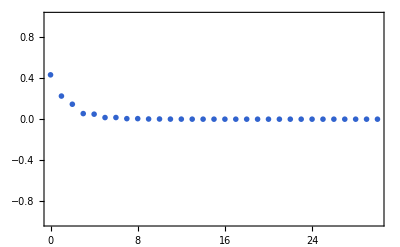

```mathematica
Block[{x= RandomReal[],y= RandomReal[],z= RandomReal[]},ListPlot[Table[{nn,Abs[Sum[(2^-n z^n HermiteH[n,x] HermiteH[n,y])/(n!),{n,0,nn}]-(ⅇ^(x^2+y^2+(-x^2-y^2+2 x y z)/(1-z^2)))/(√(1-z^2))]},{nn,0,30,1}],PlotRange->{All,{-1,1}}]]
```

```mathematica
sumRule=(f_ E^c_ √2 z^n 2^-n/n!*HermiteH[n,x_]HermiteH[n,y_]/.z->E^a_ Sqrt[zp_])->(f E^c √2(E^((-x^2-y^2+2x y z)/(1-z^2)))/(√(1-z^2))E^(x^2+y^2)/.z->E^a √zp)//PowerExpand
```

(2^(1/2-n) ⅇ^(n a_+c_) HermiteH[n,x_] HermiteH[n,y_] f_ zp_^(n/2))/(n!)→(√2 ⅇ^(c+x^2+y^2+(-x^2-y^2+2 ⅇ^a x y √zp)/(1-ⅇ^(2 a) zp)) f)/(√(1-ⅇ^(2 a) zp))

```mathematica
psi[x_,t_]=psi[n,x,t]/.sumRule/.√a_:>PowerExpand[√Factor[a]]/.1/(√a_):>1/(√Together[a])
```

-(√2 ⅇ^(-1/2 ⅈ t w-kPo^2/(2 m (w+wPo))+1/2 m w x^2+(ⅈ kPo wPo xPo)/(w+wPo)-(m w wPo xPo^2)/(2 (w+wPo))+(w (ⅈ kPo+m wPo xPo)^2)/(m (-w+wPo) (w+wPo))+(-m w x^2+(2 ⅇ^(-ⅈ t w) w x (ⅈ kPo+m wPo xPo))/(w+wPo)-(w (ⅈ kPo+m wPo xPo)^2)/(m (-w+wPo) (w+wPo)))/(1-(ⅇ^(-2 ⅈ t w) (-w+wPo))/(w+wPo))) √w (m wPo)^(1/4))/(π^(1/4) √(w+wPo) √((ⅇ^(-2 ⅈ t w) (w+ⅇ^(2 ⅈ t w) w-wPo+ⅇ^(2 ⅈ t w) wPo))/(w+wPo)))

```mathematica
psi[x,0]==psi[x,t]/.t->0/.E^q_:>E^Expand[Together[q]]//FullSimplify
```

(m wPo)^(1/4) (-1+√(1/(w+wPo)) √(w+wPo))==0

```mathematica
psi[x_,t_]:=E^(I xphase-(m wP[t](x-xP[t])^2)/2)(m wP[t]/π)^(1/4)
```

```mathematica
wPRule:=wP[t]->w^2 wPo/(w^2Cos[t w]^2+wPo^2Sin[t w]^2)
xPRule:=xP[t]->xPo Cos[t w]+kPo Sin[t w]/m/w
```

```mathematica
psisq[x_,t_]=ComplexExpand[psi[x,t]*psi[x,t]/.wPRule/.xPRule]
```

(ⅇ^(-(m w^2 wPo (x-xPo Cos[t w]-(kPo Sin[t w])/(m w))^2)/(w^2 Cos[t w]^2+wPo^2 Sin[t w]^2)) √(w^2) (m^2 wPo^2)^(1/4) Cos[1/4 Arg[m wPo]]^2 √(1/(w^2 Cos[t w]^2+wPo^2 Sin[t w]^2)))/(√π)+(ⅇ^(-(m w^2 wPo (x-xPo Cos[t w]-(kPo Sin[t w])/(m w))^2)/(w^2 Cos[t w]^2+wPo^2 Sin[t w]^2)) √(w^2) (m^2 wPo^2)^(1/4) √(1/(w^2 Cos[t w]^2+wPo^2 Sin[t w]^2)) Sin[1/4 Arg[m wPo]]^2)/(√π)

```mathematica
xExp[t_]=xP[t]/.xPRule
```

xPo Cos[t w]+(kPo Sin[t w])/(m w)

```mathematica
Clear[w,xPo,kPo,m]
```

```mathematica
pExp[t_]:=kPo Cos[t w]-m w xPo Sin[t w]
```

```mathematica
Column[Table[ListPointPlot3D[Table[Chop@Evaluate[psisq[x,t]/.{m->1,w->1,xPo->-5.,kPo->0}//N],{x,-10,10,.1},{t,0,π,π/6}],ImageSize->Medium,PlotRange->All],
{wPo,{.5,1,1.5}}]]
```

-Graphics3D-
-Graphics3D-
-Graphics3D-

quasi-classical states

eigenvalues of lowering operator is not real

```mathematica
alpha=aL@psi[x,0]/psi[x,0]/.wPo->w/.h->1//Expand
```

(ⅈ kPo √(m w))/(√2 m w)+(√(m w) xPo)/(√2)

in fact, it can be any value since it determines the classical energy of HO

```mathematica
w alpha*alpha//ComplexExpand//FullSimplify
```

(kPo^2+m^2 w^2 xPo^2)/(2 m)

Non-Hermiticity also means that two coherent states belonging to two different eigenvalues are not orthogonal. The distance between two eigenvalues in the complex plane determines the degree of orthogonality.

#### basic matrix mechanics & partial exact diagonalization (due to truncation)

represent operator in terms of its integrals between a complete set of wavefunctions

The barriers give rise to special continuum states having much in common with bound states: metastable/resonance states

Discrete-energy basis functions used to approximate a continuum are called pseudo-continuum states.

model-Hamiltonian matrix

```mathematica
psi[n_,z_]:=Sum[psiHOz[k,z]c[k,n],{k,0,nmax}]
```

```mathematica
c[k_,n_]:=cvec[n][[k+1]]
```

```mathematica
VPme[n_,k_]:=VPme[n,k]=
If[OddQ[n+k],0,
Integrate[
psiHOz[n,z](V-VHO)psiHOz[k,z],{z,-Infinity,Infinity}]//N]
VPme[k_,n_]:=VPme[n,k]/;k>n
```

```mathematica
nmax=4;
hMatrix=Table[
(Vo+n+1/2)KroneckerDelta[n,k]+VPme[n,k],{n,0,nmax},{k,0,nmax}];
hMatrix//MatrixForm
```

(-1.44023 | 0 | 0.0336936 | 0 | -0.0524215
0 | -0.392579 | 0 | -0.0464838 | 0
0.0336936 | 0 | 0.526665 | 0 | -0.19011
0 | -0.0464838 | 0 | 1.3451 | 0
-0.0524215 | 0 | -0.19011 | 0 | 2.08463)

weakly interacting energy levels

levels included are well separated in energy from those excluded, or if the interaction matrix elements between the two sets of levels are small, or optimally, both.

```mathematica
{es,cvecs}=Chop@Transpose[Sort[Transpose[Eigensystem[hMatrix]]]]
```

{{-1.4415,-0.393822,0.504182,1.34634,2.10838},{{0.999778,0,-0.015762,0,0.0140135},{0,0.999643,0,0.0267219,0},{0.01397,0,0.992691,0,0.119872},{0,-0.0267219,0,0.999643,0},{-0.0158005,0,-0.11965,0,0.99269}}}

```mathematica
e[n_]:=es[[n+1]]
cvec[n_]:=cvecs[[n+1]]
```

```mathematica
Table[cvec[n].cvec[k],{n,0,nmax},{k,0,nmax}]//Chop//MatrixForm
```

(1. | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0
0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 1.)

```mathematica
Table[Chop@hMatrix.cvec[n]==Chop@e[n]cvec[n],{n,0,nmax}]
```

{True,True,False,True,True}

```mathematica
ReleaseHold[Hold[Norm[Abs[Chop@hMatrix.cvec[n]-Chop@e[n]cvec[n]]]]/.n->2]
```

5.02531×10^-16

```mathematica
psi[0,z]
```

-0.750958 ⅇ^(-z^2/2)+0.00418579 ⅇ^(-z^2/2) (-2+4 z^2)-0.000537146 ⅇ^(-z^2/2) (12-48 z^2+16 z^4)

```mathematica
Show[Plot[Table[Evaluate[(1/2+i)-psiHO[i,x]/.{h->1,w->1,m->1}//N],{i,0,5}],{x,-6,6}],Plot[Table[Evaluate[(1/2+i)],{i,0,5}],{x,-6,6},PlotStyle->Dashed],
Plot[Evaluate[VHO/.{h->1,w->1,m->1}//N],{x,-6,6},PlotStyle->Dashed]]
```

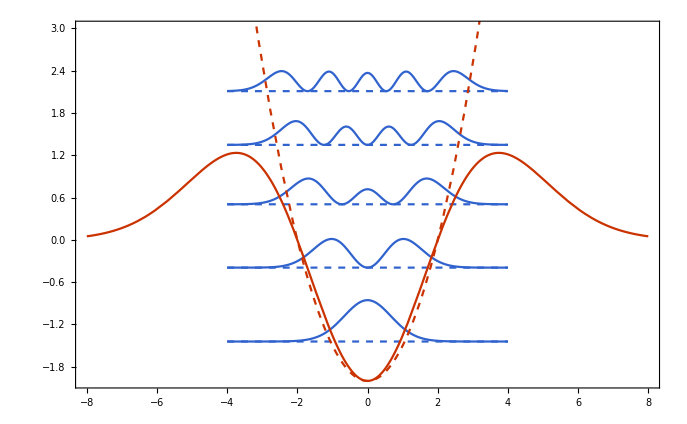

```mathematica
Show[Plot[Table[e[n]+psi[n,z]^2,{n,0,nmax}],{z,-4,4},PlotRange->{{-8,8},{-2,3}}],Plot[Table[e[n],{n,0,nmax}],{z,-4,4},PlotStyle->Dashed],Plot[{V,VHO},{z,-8,8},PlotStyle->{Directive[Red],Directive[Dashed,Red]}]]
```

```mathematica
1==Integrate[psi[0,z]^2,{z,-Infinity,Infinity}]//Chop
```

True

local energy

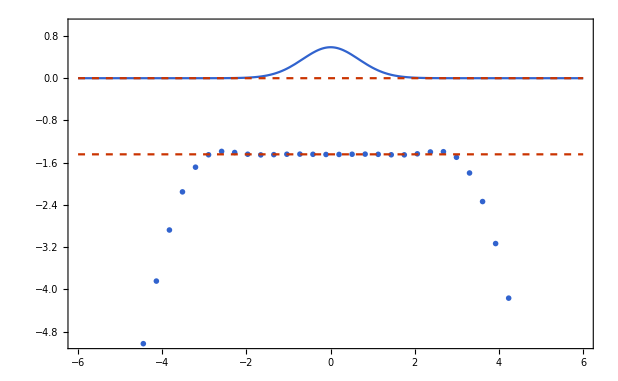

```mathematica
ha[V_]@psi_:=-1/2D[psi,{z,2}]+V psi
V=VHO E^(-b z^2);b=.1;
VHO=Vo+z^2/2;Vo=-2;
Show[Plot[{psi[0,z]^2,0},{z,-6,6},PlotRange->{All,{-5,1}},PlotStyle->{Default,Dashed}],ListPlot[Table[{z,ha[V]@psi[n,z]/psi[n,z]}//Table[#,{z,-6,6,.31}]&,{n,{0}}],PlotRange->All],Plot[e[0],{x,-6,6},PlotStyle->{Red,Dashed}]]
```

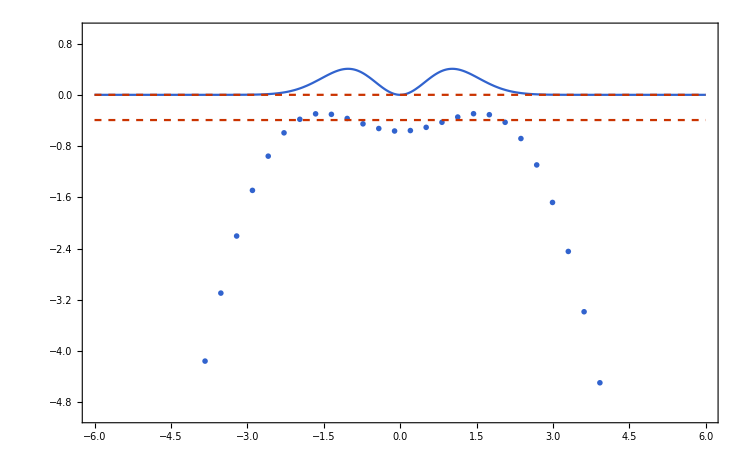

```mathematica
Show[Plot[{psi[1,z]^2,0},{z,-6,6},PlotRange->{All,{-5,1}},PlotStyle->{Default,Dashed}],ListPlot[Table[{z,ha[V]@psi[n,z]/psi[n,z]}//Table[#,{z,-6,6,.31}]&,{n,{1}}],PlotRange->All],Plot[e[1],{x,-6,6},PlotStyle->{Red,Dashed}]]
```

```mathematica
nmax=8;
hMatrix=Table[
(Vo+n+1/2)KroneckerDelta[n,k]+VPme[n,k],{n,0,nmax},{k,0,nmax}];
{es,cvecs}=Transpose[Sort[Transpose[-Eigensystem[-hMatrix,2,Method->{"Arnoldi","Criteria"->"RealPart",MaxIterations->10^6}]]]]
```

{{-1.4415,-0.398051},{{-0.999776,-1.0265×10^-16,0.0157503,2.20759×10^-16,-0.0141022,1.22525×10^-16,-0.00017232,-2.28962×10^-16,-0.00081179},{-1.7721×10^-16,0.998621,8.8749×10^-17,0.0356294,-8.88812×10^-18,0.0381137,1.80754×10^-16,0.00580898,2.05931×10^-17}}}

local energy should be nearly constant and equal to the corresponding perturbed eigenvalue, at least for the region where the probability density is nonvanishing. It is acceptable that the local energy diverges from perturbed eigenvalue in the tails of the wavefunction, since the error won’t contribute significantly to the energy expectation value.

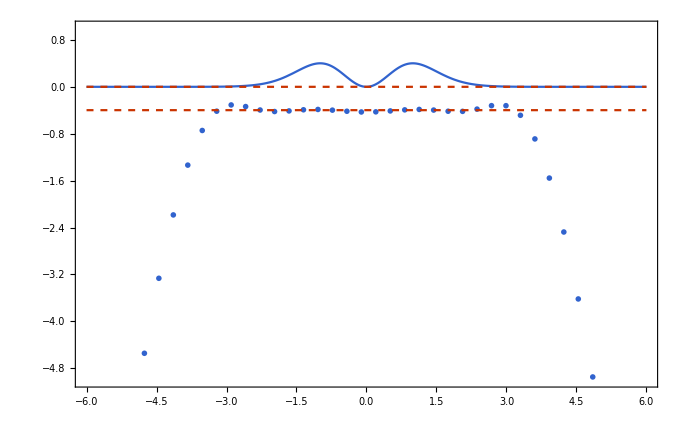

```mathematica
Show[Plot[{psi[1,z]^2,0},{z,-6,6},PlotRange->{All,{-5,1}},PlotStyle->{Default,Dashed}],ListPlot[Table[{z,ha[V]@psi[n,z]/psi[n,z]}//Table[#,{z,-6,6,.31}]&,{n,{1}}],PlotRange->All],Plot[e[1],{x,-6,6},PlotStyle->{Red,Dashed}]]
```

pseudo states and resonances

a resonance level below the barriers may behave like a bound state inside the well, while behave like a free particle far from the center of force. Resonances above/below the barriers arise from multiple reflections of the wavefunction off the barriers (off the impedance mismatch), which are in phase and hence constructively interfere.

diagonalization

```mathematica
cMatrix=Transpose[Table[cvec[i],{i,0,nmax}]];
```

```mathematica
Transpose[cMatrix].cMatrix//Chop//MatrixForm
```

(1. | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0
0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 1.)

similarity transformation

```mathematica
Transpose[cMatrix].hMatrix.cMatrix//Chop//MatrixForm
```

(-1.4415 | 0 | 0 | 0 | 0
0 | -0.393822 | 0 | 0 | 0
0 | 0 | 0.504182 | 0 | 0
0 | 0 | 0 | 1.34634 | 0
0 | 0 | 0 | 0 | 2.10838)

```mathematica
DiagonalMatrix[es]//MatrixForm
```

(-1.4415 | 0. | 0. | 0. | 0.
0. | -0.393822 | 0. | 0. | 0.
0. | 0. | 0.504182 | 0. | 0.
0. | 0. | 0. | 1.34634 | 0.
0. | 0. | 0. | 0. | 2.10838)

#### momentum representation

the coefficients of the plane wave components are determined by the Fourier transform of the wave packet as a function of k

Fourier transform pairs (the sign conventions of exponents are usually reversed in engineering applications)

```mathematica
FT[psi_,x_][k_]:=1/(√(2π))Integrate[psi E^(-I k x),{x,-Infinity,Infinity}]
InvFT[phi_,k_][x_]:=1/(√(2π))Integrate[phi E^(I k x),{k,-Infinity,Infinity}]
```

```mathematica
FT[E^(-w x^2),x][k]//FullSimplify
```

(ⅇ^(-k^2/(4 w)))/(√2 √w)

```mathematica
InvFT[%,k][x]//FullSimplify
```

ⅇ^(-w x^2)

```mathematica
psi[x_]:=(w/π)^(1/4)E^(-w x^2/2)
```

```mathematica
phi[k_]=FT[psi[x],x][k]//FullSimplify
```

(ⅇ^(-k^2/(2 w)))/(π^(1/4) w^(1/4))

```mathematica
psi[x]==Integrate[phi[k]E^(I k x)/√(2π),{k,-Infinity,Infinity}]//FullSimplify
```

True

HO momentum wavefunctions

```mathematica
phiHO[n_,k_]:=phiHO[n,k]=FT[psiHO[n,x],x][k]
phiHOkz[n_,kz_]:=phiHOkz[n,kz]=FT[psiHOz[n,z],z][kz]
```

```mathematica
{phiHO[0,k],phiHO[1,k]}//FullSimplify
```

{-(ⅇ^(-(h k^2)/(2 m w)))/(π^(1/4) ((m w)/h)^(1/4)),(ⅈ √2 ⅇ^(-(h k^2)/(2 m w)) k (h/(m w))^(3/4))/π^(1/4)}

```mathematica
{phiHOkz[0,kz],phiHOkz[1,kz]}//FullSimplify
```

{-(ⅇ^(-kz^2/2))/π^(1/4),(ⅈ √2 ⅇ^(-kz^2/2) kz)/π^(1/4)}

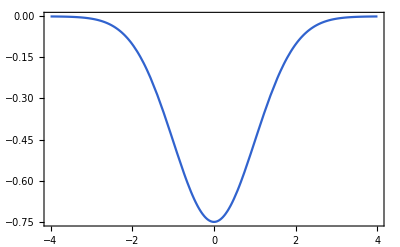

```mathematica
Plot[-(ⅇ^(-kz^2/2))/π^(1/4),{kz,-4,4},PlotRange->All]
```

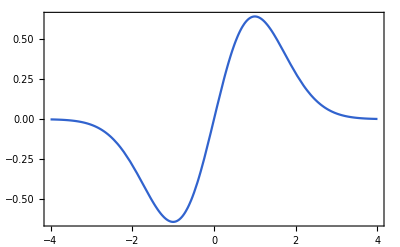

```mathematica
Plot[Im[(ⅈ √2 ⅇ^(-kz^2/2) kz)/π^(1/4)],{kz,-4,4},PlotRange->All]
```

```mathematica
Table[Integrate[phiHO[np,k]*phiHO[n,k],{k,-Infinity,Infinity}],{np,0,1},{n,0,1}]//MatrixForm
```

(1 | 0
0 | 1)

Dirac Delta Function

```mathematica
{psiHO[0,xo]==InvFT[FT[psiHO[0,x],x][k],k][xo],psiHO[1,xo]==InvFT[FT[psiHO[1,x],x][k],k][xo]}//FullSimplify
```

{True,True}

```mathematica
psi[xo]==Integrate[psi[x]DiracDelta[x-xo],{x,-Infinity,Infinity}]
```

ConditionalExpression[True,xo∈ℝ]

```mathematica
DiracDelta[x-xo]==1/(2π)Integrate[E^(I k(x-xo)),{k,-Infinity,Infinity},Assumptions->x∈Reals&&xo∈Reals]
```

Integrate::idiv: Integral of ⅇ^(ⅈ k (x-xo)) does not converge on {-∞,∞}.

DiracDelta[x-xo]==Integrate[ⅇ^(ⅈ k (x-xo)),{k,-∞,∞},Assumptions→x∈ℝ&&xo∈ℝ]/(2 π)

```mathematica
integrate[f_. DiracDelta[x_+xo_.],{x_,-Infinity,Infinity}]:=f/.x->-xo
```

```mathematica
Clear[f]
integrate[f[x]DiracDelta[x-xo],{x,-Infinity,Infinity}]
```

f[xo]

```mathematica
integrate[DiracDelta[x],{x,-Infinity,Infinity}]
```

1

#### lattice representation

```mathematica
{nmax=2^5,L=12.0,dz=L/nmax}
```

{32,12.,0.375}

```mathematica
zGrid=Table[-L/2+(n-1)dz,{n,nmax}]
```

{-6.,-5.625,-5.25,-4.875,-4.5,-4.125,-3.75,-3.375,-3.,-2.625,-2.25,-1.875,-1.5,-1.125,-0.75,-0.375,0.,0.375,0.75,1.125,1.5,1.875,2.25,2.625,3.,3.375,3.75,4.125,4.5,4.875,5.25,5.625}

we take nmax to be even for built-in FFT, due to the same reason, we take dz corresponds to a lattice with an odd number of points nmax+1 in order to include the origin z=0.

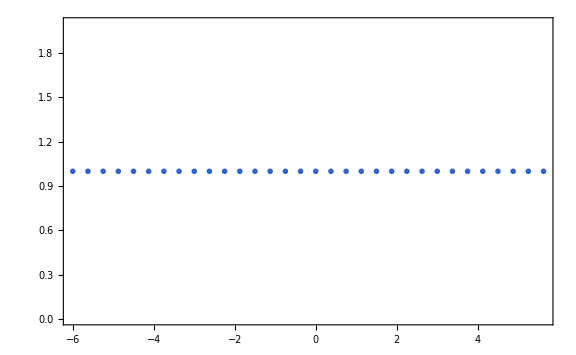

```mathematica
ListPlot[{zGrid,ConstantArray[1,nmax]}ᵀ,ImageSize->Large]
```

{-1.14396×10^-8,-1.01167×10^-7,-7.77305×10^-7,-5.18887×10^-6,-0.0000300941,-0.000151641,-0.000663865,-0.00252505,-0.00834425,-0.023957,-0.0597592,-0.12951,-0.243855,-0.39892,-0.566979,-0.700126,-0.751126,-0.700126,-0.566979,-0.39892,-0.243855,-0.12951,-0.0597592,-0.023957,-0.00834425,-0.00252505,-0.000663865,-0.000151641,-0.0000300941,-5.18887×10^-6,-7.77305×10^-7,-1.01167×10^-7}

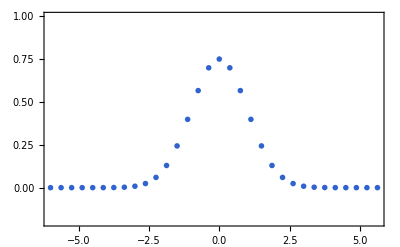

```mathematica
psiHOzGrid[0]=psiHOz[0,zGrid]//N
ListPlot[{zGrid,-%}ᵀ,PlotRange->{-.2,1}]
```

```mathematica
psiHOzGrid[i_]:=psiHOz[i,zGrid]//N
```

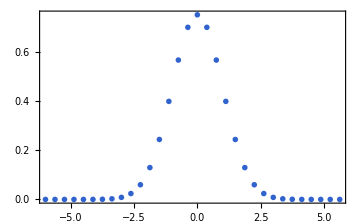
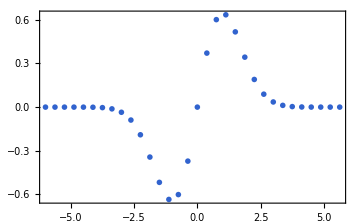
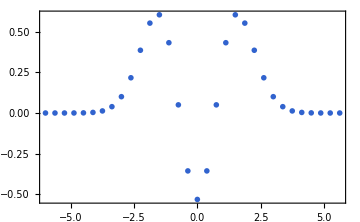

```mathematica
Row[Table[ListPlot[{zGrid,-psiHOzGrid[i]}ᵀ,ImageSize->Medium],{i,0,2}]]
```

Note:
L large enough to includes the tails.
nmax large enough to capture all “wiggles” in the wavefunctions, i.e., dz = L/nmax is fine enough to resolve all the structure in the wavefunction.

trapezoidal integration rule

```mathematica
psiHOzGrid[0].psiHOzGrid[0]dz
```

1.

```mathematica
Table[psiHOzGrid[i].psiHOzGrid[j]dz,{i,0,2},{j,0,2}]//Chop//MatrixForm
```

(1. | 0 | 0
0 | 1. | 0
0 | 0 | 1.)

momentum lattice

The Fourier series assume psi[z+L]==psi[z]. Then the planewve components E^(+/- I kz z) is the Fourier integrals to have the same periodicity, i.e., kz=q dkz where q∈ℤ and dkz=2π/L

```mathematica
{dkz=2π/L//N,kzmax=nmax/2 dkz}
```

{0.523599,8.37758}

```mathematica
kzGrid=Table[-kzmax+(q-1)dkz,{q,1,nmax}]
```

{-8.37758,-7.85398,-7.33038,-6.80678,-6.28319,-5.75959,-5.23599,-4.71239,-4.18879,-3.66519,-3.14159,-2.61799,-2.0944,-1.5708,-1.0472,-0.523599,0.,0.523599,1.0472,1.5708,2.0944,2.61799,3.14159,3.66519,4.18879,4.71239,5.23599,5.75959,6.28319,6.80678,7.33038,7.85398}

```mathematica
kzmax==π/dz//N
```

True

```mathematica
phiHOkzGrid[i_]:=phiHOkz[i,kz]/.kz->kzGrid//N
```

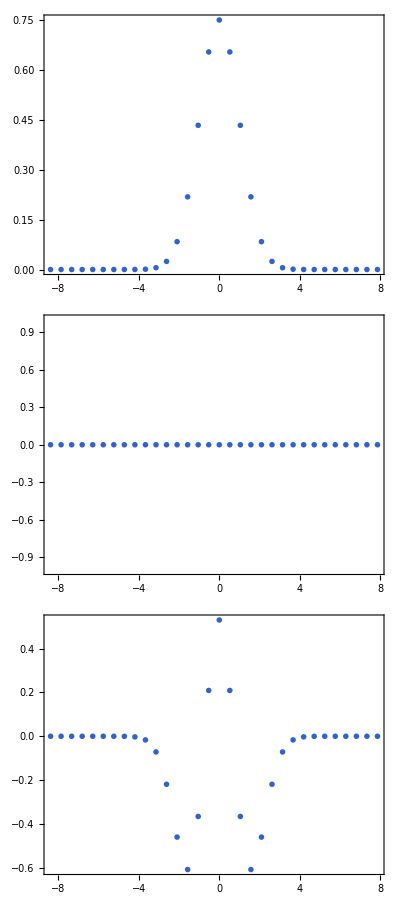

```mathematica
Column[Table[ListPlot[{kzGrid,-Re@phiHOkzGrid[i]}ᵀ,ImageSize->Medium,PlotRange->All],{i,0,2}]]
```

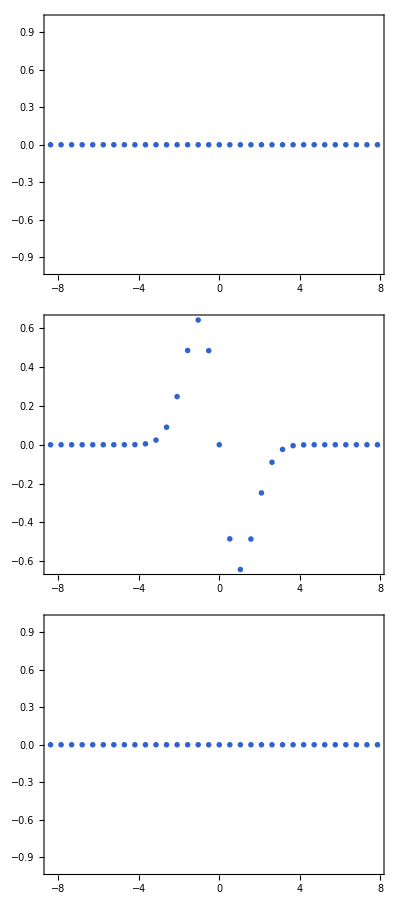

```mathematica
Column[Table[ListPlot[{kzGrid,-Im@phiHOkzGrid[i]}ᵀ,ImageSize->Medium,PlotRange->All],{i,0,2}]]
```

nmax → kzmax
L → dkz
dz dkz == 2π/nmax
to check nmax, go the Fourier space

```mathematica
FTGrid[psizGrid_]:=
Table[
Sum[E^(-I kzGrid[[q]]zGrid[[n]])psizGrid[[n]],{n,nmax}] dz/(√(2π))//N,{q,nmax}]
InvFTGrid[phikzGrid_]:=
Table[
Sum[E^(I kzGrid[[q]]zGrid[[n]])phikzGrid[[q]],{q,nmax}] dkz/(√(2π))//N,{n,nmax}]
```

```mathematica
FTGrid[psiHOzGrid[0]]//Chop
```

{1.40184×10^-9,-1.40647×10^-9,1.41861×10^-9,-1.5084×10^-9,-5.34474×10^-10,-4.85399×10^-8,-8.34997×10^-7,-0.0000113154,-0.000116318,-0.000909155,-0.00540201,-0.0244011,-0.0837911,-0.218737,-0.434094,-0.654908,-0.751126,-0.654908,-0.434094,-0.218737,-0.0837911,-0.0244011,-0.00540201,-0.000909155,-0.000116318,-0.0000113154,-8.34997×10^-7,-4.85399×10^-8,-5.34474×10^-10,-1.5084×10^-9,1.41861×10^-9,-1.40647×10^-9}

```mathematica
Norm[%-phiHOkzGrid[0]]
```

9.77485×10^-9

aliasing -> reduced by letting kzmax^2/2+Vmax large comparing to energy of the wavefunctions we are studying

```mathematica
Sin[kzmax]
```

0.866025

```mathematica
psiHOzGrid[0]-InvFTGrid[FTGrid[psiHOzGrid[0]]]//Norm
```

2.93991×10^-15

```mathematica
InvFTGrid[I kzGrid FTGrid[E^(-zGrid^2)]]-(D[E^(-z^2),z]/.z->zGrid)//Norm
```

3.39393×10^-7

local energy

```mathematica
Elocal[0]=InvFTGrid[kzGrid^2/2FTGrid[psiHOzGrid[0]]]/psiHOzGrid[0]+zGrid^2/2//Chop
```

{-27.3477-2.35762×10^-8 ⅈ,0.943684+5.10767×10^-10 ⅈ,0.480801-8.25863×10^-10 ⅈ,0.50139,0.499859,0.500019,0.499997,0.500001,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.500001,0.499997,0.500019,0.499859,0.50139,0.480801+7.8618×10^-10 ⅈ,0.943684-3.48222×10^-10 ⅈ}

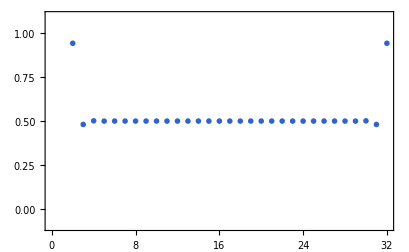

```mathematica
ListPlot[Chop[Elocal[0],10^-5],PlotRange->{-.1,1.1}]
```

```mathematica
(psiHOzGrid[0]^2).Elocal[0]dz
```

0.5-9.52433×10^-24 ⅈ

#### FFT

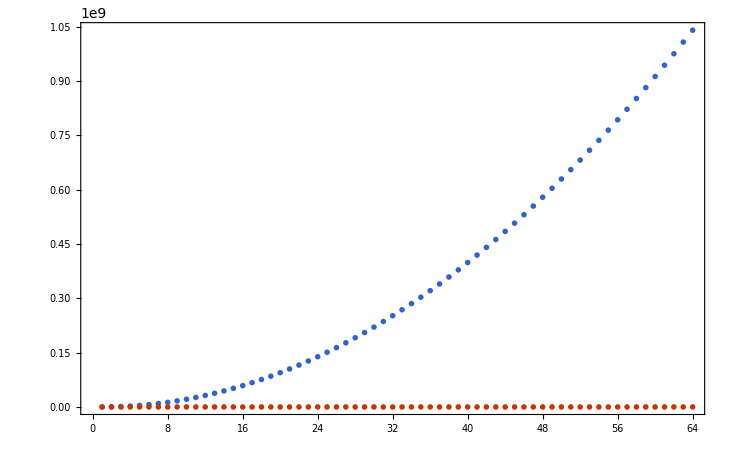

```mathematica
ListPlot[Table[{n^2,n Log[n,2]},{n,2,2^15,2^9}]ᵀ,PlotRange->All]
```

```mathematica
psiHOzGrid[0]-InverseFourier[Fourier[psiHOzGrid[0]]]//Norm
```

3.93104×10^-16

F and IF take the lattice origin of their argument list to be at the left end of the lattice, i.e., at the first element of the argument list.
We need to shift or rotate our lattice wavefunctions by half a lattice length.
If applying an operator, we can also simply shift the lattice representation of the operator instead

```mathematica
kzpGrid=kzGrid//RotateLeft[#,nmax/2]&
```

{0.,0.523599,1.0472,1.5708,2.0944,2.61799,3.14159,3.66519,4.18879,4.71239,5.23599,5.75959,6.28319,6.80678,7.33038,7.85398,-8.37758,-7.85398,-7.33038,-6.80678,-6.28319,-5.75959,-5.23599,-4.71239,-4.18879,-3.66519,-3.14159,-2.61799,-2.0944,-1.5708,-1.0472,-0.523599}

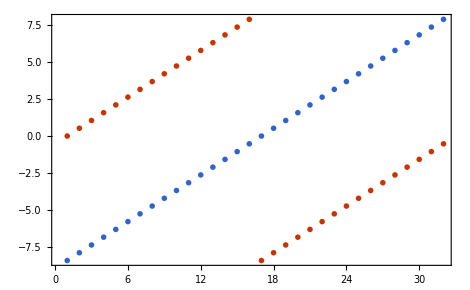

```mathematica
ListPlot[{kzGrid,kzpGrid},PlotRange->All]
```

```mathematica
ElocalFFT[0]=InverseFourier[kzpGrid^2/2Fourier[psiHOzGrid[0]]]/psiHOzGrid[0]+zGrid^2/2//Chop
```

{-27.3477+8.25566×10^-9 ⅈ,0.943684+1.64976×10^-9 ⅈ,0.480801-2.20928×10^-10 ⅈ,0.50139,0.499859,0.500019,0.499997,0.500001,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.500001,0.499997,0.500019,0.499859,0.50139,0.480801+4.93825×10^-10 ⅈ,0.943684-3.51718×10^-9 ⅈ}

```mathematica
(Elocal[0]-ElocalFFT[0])//Norm
```

5.3002×10^-8

```mathematica
(psiHOzGrid[0]^2).ElocalFFT[0]dz//Chop
```

0.5

#### wave packet propagation

```mathematica
{nmax=2^7,L=20.0,dz=L/nmax,dkz=N[2π/L],kzmax=N[π/dz]}
```

{128,20.,0.15625,0.314159,20.1062}

```mathematica
zGrid=Table[-L/2+(n-1)dz,{n,nmax}];
kzGrid=Table[-kzmax+(q-1)dkz,{q,nmax}];
kzpGrid=kzGrid//RotateLeft[#,nmax/2]&;
```

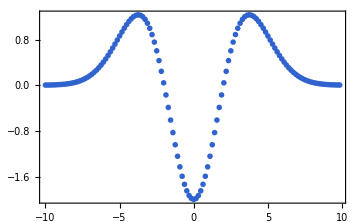

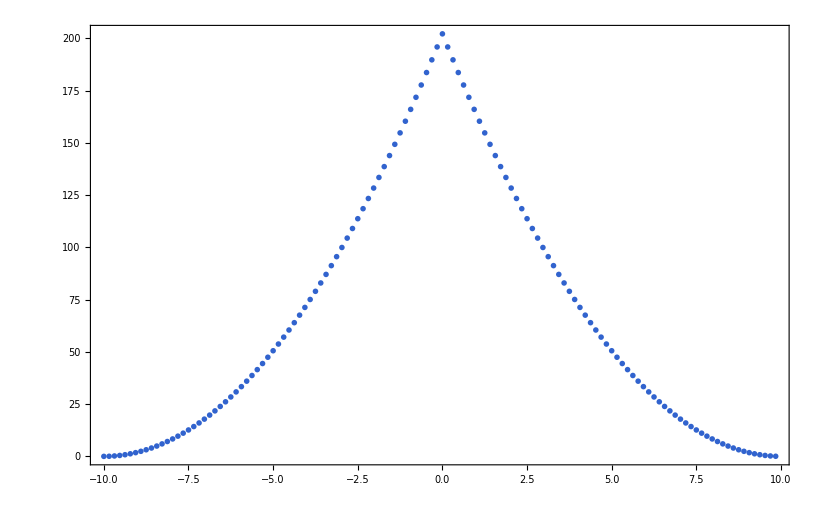

```mathematica
Clear[V,VHO];
Vmodel[z_]:=VHO[z] E^(-b z^2);b=.1;
VHO[z_]:=Vo+z^2/2;Vo=-2.0;
V=Vmodel[zGrid];
(* use kzpGrid instead of kzGrid! *)
K=kzpGrid^2/2;
ListPlot[{zGrid,V}ᵀ,PlotRange->All,ImageSize->Medium]
ListPlot[{zGrid,K}ᵀ]
```

```mathematica
{ntmax=2000,T=10.0,dt=T/ntmax}
```

{2000,10.,0.005}

```mathematica
U[dt_]@psi_:=UV[dt]InverseFourier[UK[dt]Fourier[psi]]
UV[dt]=E^(-I V dt);
UK[dt]=E^(-I K dt);
psi[nt_,psi0_]:=Nest[U[dt][#]&,psi0,nt]
```

```mathematica
eExp[psi_]:=Conjugate[psi].H@psi/Conjugate[psi].psi
dele[psi_]:=Conjugate[psi].H@H@psi/Conjugate[psi].psi-eExp[psi]^2//Sqrt
H@psi_:=InverseFourier[K Fourier[psi]]+V psi
```

```mathematica
psi[0]=E^(I kPo z)E^(-wPo z^2/2)(wPo/π)^(1/4)/.{kPo->1.0,wPo->2.0}/.z->zGrid//N;
```

```mathematica
(* note the ordering of F(IF()) in the last element *)
{psi[0]*.psi[0]dz,psi[0]*.(zGrid psi[0])dz,psi[0]*.Fourier[kzpGrid InverseFourier[psi[0]]]dz}//Chop
```

{1.,0,1.}

```mathematica
{eExp[psi[0]],dele[psi[0]]}//Chop
```

{-0.835622,1.11319}

time development

```mathematica
Do[psi[nt]=psi[10,psi[nt-10]],{nt,10,ntmax,10}]
```

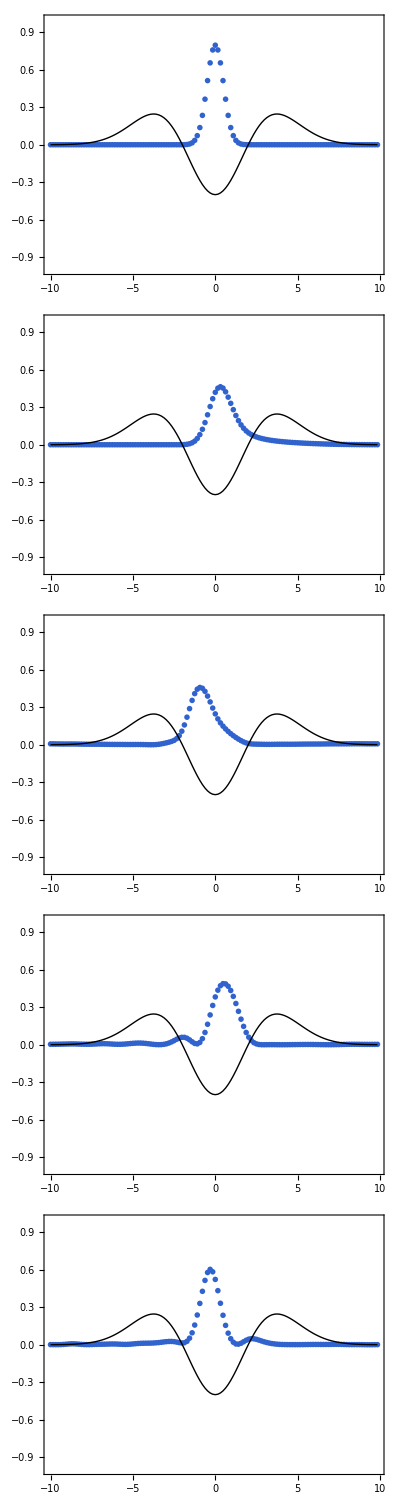

```mathematica
{ntmax=2000*4,T=10.0,dt=T/ntmax};
U[dt_]@psi_:=UV[dt]InverseFourier[UK[dt]Fourier[psi]]
UV[dt]=E^(-I V dt);
UK[dt]=E^(-I K dt);
psi[nt_,psi0_]:=Nest[U[dt][#]&,psi0,nt]
eExp[psi_]:=Conjugate[psi].H@psi/Conjugate[psi].psi
dele[psi_]:=Conjugate[psi].H@H@psi/Conjugate[psi].psi-eExp[psi]^2//Sqrt
H@psi_:=InverseFourier[K Fourier[psi]]+V psi
psi[0]=E^(I kPo z)E^(-wPo z^2/2)(wPo/π)^(1/4)/.{kPo->1.0,wPo->2.0}/.z->zGrid//N;
Do[psi[nt]=psi[10,psi[nt-10]],{nt,10,ntmax,10}];
Column@Table[ListPlot[{zGrid,Abs[psi[i]]^2}ᵀ,Epilog->{Line[Thread[{zGrid,1/5 V}]]},ImageSize->Medium,PlotRange->{-1,1}],{i,0,ntmax,ntmax/4}]
```

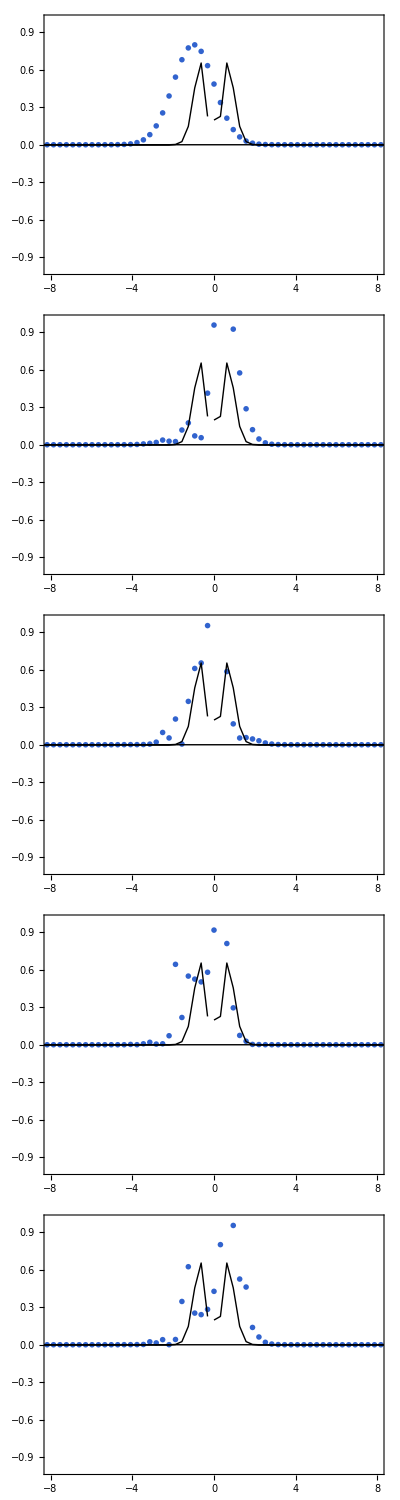

```mathematica
Column@Table[ListPlot[{kzpGrid,Abs[Fourier[psi[i]]]^2}ᵀ,Epilog->{Line[Thread[{kzpGrid,1/8 Abs[Fourier@V]}]]},ImageSize->Medium,PlotRange->{{-8,8},{-1,1}}],{i,0,ntmax,ntmax/4}]
```

correlation function

```mathematica
c[Cpsi0_,psit_]:=Cpsi0.psit dz
```

set up a procedure to collect together and evaluate all quantities while propagating the wave packets as a function of time.

```mathematica
TimeDevelopment[ntmax_,psi0_]:=
Module[
{psit=psi0,Cpsi0=psi0*},
c[t]={};
zExp={};zsqExp={};kzExp={};kzsqExp={};
Do[
AppendTo[c[t],c[Cpsi0,psit]];
AppendTo[zExp,dz psit*.(zGrid psit)];
AppendTo[zsqExp,dz psit*.(zGrid^2 psit)];
AppendTo[kzExp,dz psit*.Fourier[kzpGrid InverseFourier[psit]]];
AppendTo[kzsqExp,dz psit*.Fourier[kzpGrid^2InverseFourier[psit]]
];
psit=U[dt]@psit,
{ntmax}
]
]
```

```mathematica
{ntmax=2^11,T=60.0,dt=T/ntmax}
```

{2048,60.,0.0292969}

```mathematica
UV[dt]=E^(-I V dt);UK[dt]=E^(-I K dt);
tGrid=Table[(nt-1)dt,{nt,ntmax}];
```

```mathematica
TimeDevelopment[ntmax,psi[0]]
```

```mathematica
SetOptions[ListPlot,ImageSize->300];
```

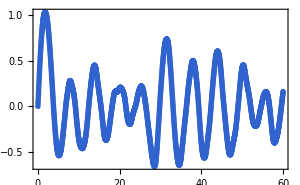

```mathematica
ListPlot[{tGrid,zExp}ᵀ,PlotRange->All]
```

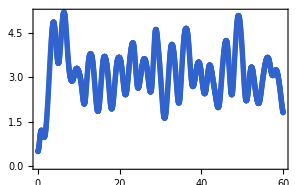

```mathematica
ListPlot[{tGrid,kzsqExp zsqExp}ᵀ,PlotRange->All]
```

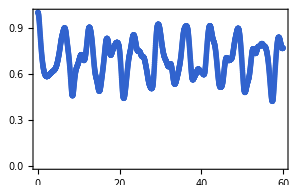

```mathematica
ListPlot[{tGrid,Abs[c[t]]}ᵀ,PlotRange->All]
```

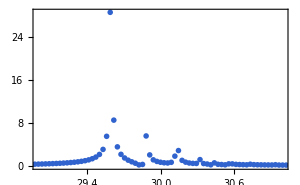

```mathematica
ListPlot[{wtpGrid,Abs[Fourier@c[t]]}ᵀ,PlotRange->{{29,31},All}]
```

```mathematica
{dwz=N[2π/T],wtmax=N[π/dt]}
```

{0.10472,107.233}

```mathematica
wtGrid=Table[0+(q-1)dt,{q,ntmax}];
wtpGrid=wtGrid//RotateLeft[#,ntmax/2]&;
```

energy spectrum

c[t] = sum[Abs[a[n]]^2 E^(-I e[n] t), {n}]
sum over discrete bound states and integration over the continuum states.
FT of correlation function yields the energy spectrum, in the sense that it is peaked there.
discrete FT means replacing the delta functions in the spectrum by functions of finite width. Works best for well-separated bound and resonance states.

```mathematica
(* have middle of the lattice correspond to zero energy *)
cFT[e]=Fourier[c[t]]//RotateLeft[#,ntmax/2]&;
```

```mathematica
{de=N[2π/T],emax=N[π/dt]}
```

{0.10472,107.233}

```mathematica
(* after having the middle of the lattice with zero energy, we simply construct the lattice as usual *)
eGrid=Table[-emax+(qe-1)de,{qe,1,ntmax}];
```

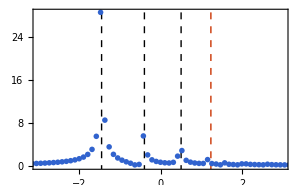

```mathematica
ListPlot[{eGrid,Abs[cFT[e]]}ᵀ,PlotRange->{{-3,3},All},
Epilog->{Table[{Dashed,InfiniteLine[{e[i],0},{0,1}]},{i,0,2}],
{Dashed,Red,InfiniteLine[{Max[V],0},{0,1}]}}]
```

The peaks are two bound states and first resonance we estimated by diagonalization before.
Note the appearance of the second resonance state below the top of the potential barriers!
Other weaker resonances are also discernable above the barriers.

#### quantum diffusion (diffusion filtering)

time-propagation scheme can be used to obtain eigenenergies and eigenfunctions, using FT of the correlation function.
For the ground state, a simple way to improve the convergence and accuracy is to replace the time t by tC = I*t and solve a classical diffusion equation,

-D[psi[z, tC], tC] == ha[V]@psi[z, tC]

```mathematica
{ntmax=400,T=4.0,dtC=T/ntmax}
```

{400,4.,0.01}

```mathematica
tCGrid=Table[(nt-1)dtC,{nt,ntmax}];
UV[dtC]=E^(-V dtC);UK[dtC]=E^(-K dtC);
```

```mathematica
?Random
```

```mathematica
psi[0]=Table[Random[],{nmax}];
```

```mathematica
U[dt_]@psi_:=UV[dt]InverseFourier[UK[dt]Fourier[psi]]
psi[nt_,psi0_]:=Nest[U[dtC][#]&,psi0,nt]
```

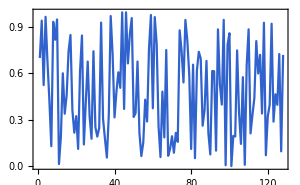

```mathematica
ListLinePlot[psi[0],PlotRange->All]
```

```mathematica
Do[psi[nt]=psi[10,psi[nt-10]],{nt,10,ntmax,10}]
```

```mathematica
SetOptions[ListLinePlot,ImageSize->300];
```

```mathematica
Vbkgrd=Epilog->{Dashed,
Line[Thread[{zGrid,1/10 V}]]
};
```

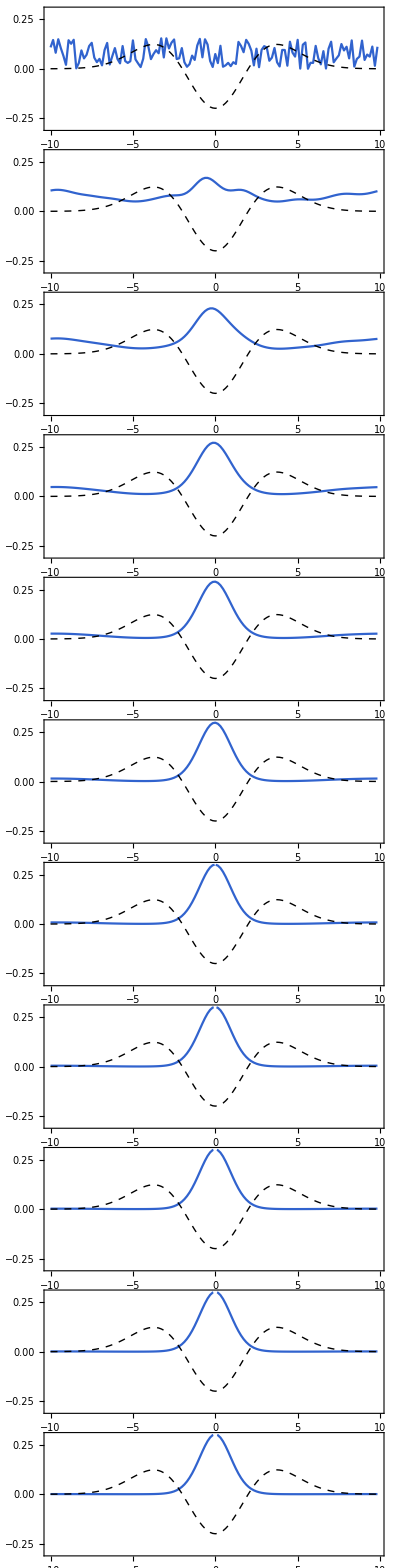

```mathematica
Column[Table[ListLinePlot[{zGrid,Abs[Normalize[psi[i]]]}ᵀ,PlotRange->{-.3,.3},
Vbkgrd
],{i,0,ntmax,40}]]
```

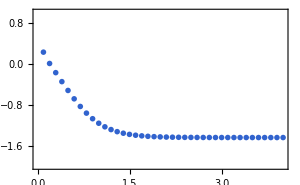

```mathematica
ListPlot[Table[{tCGrid[[nt]],eExp[psi[nt]]},{nt,10,ntmax,10}]//Chop,PlotRange->{-2,1}]
```

```mathematica
Table[eExp[psi[nt]],{nt,ntmax-50,ntmax,10}]//Chop
```

{-1.44137,-1.4414,-1.44142,-1.44144,-1.44145,-1.44146}

```mathematica
e[0]
```

-1.4415

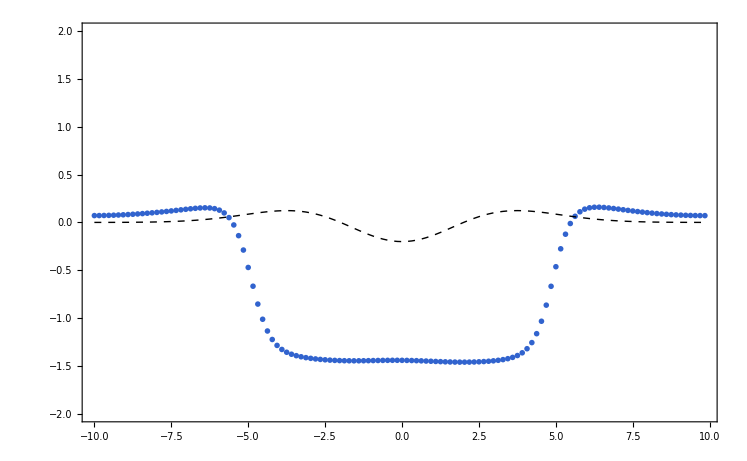

```mathematica
ListPlot[
Thread[{zGrid,H@psi[ntmax]/psi[ntmax]}]//Chop,
PlotRange->{-2,2},Vbkgrd]
```

excited states

```mathematica
project[psi_,phi_]:=psi-phi phi*.psi dz
```

```mathematica
psi1st[nt_,psi0_]:=Nest[project[U[dtC][#],psiGrd]&,psi0,nt]
psiGrd=Normalize[psi[ntmax]]/√dz;
```

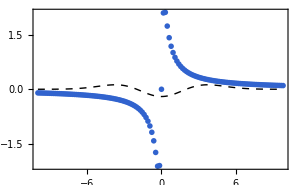

```mathematica
psi1st[0]=zGrid/(.05+zGrid^2);
ListPlot[{zGrid,psi1st[0]}ᵀ,PlotRange->All,Vbkgrd]
```

```mathematica
Do[psi1st[nt]=psi1st[10,psi1st[nt-10]],{nt,10,ntmax,10}]
```

```mathematica
Table[eExp[psi1st[nt]],{nt,ntmax-40,ntmax,10}]//Chop
```

{-0.397961,-0.397984,-0.398005,-0.398023,-0.398038}

```mathematica
e[1]
```

-0.393822

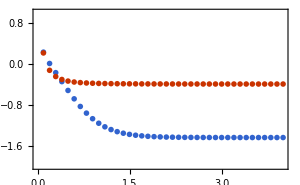

```mathematica
ListPlot[{Table[{tCGrid[[nt]],eExp[psi[nt]]},{nt,10,ntmax,10}]//Chop,Table[{tCGrid[[nt]],eExp[psi1st[nt]]},{nt,10,ntmax,10}]//Chop},PlotRange->{-2,1}]
```

#### Morse oscillator

```mathematica
Clear[b,x];
V=-De+De(1-E^(-b x))^2//Expand
```

De ⅇ^(-2 b x)-2 De ⅇ^(-b x)

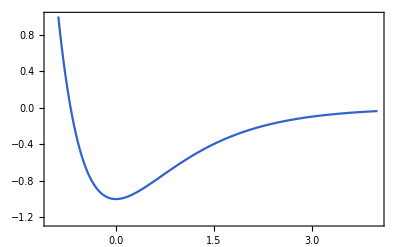

```mathematica
Plot[V/De/.{x->y/b},{y,-1,4},PlotRange->{-1.25,1}]
```

```mathematica
sD[V_]@psi_:=
-h^2/2/m D[psi,{x,2}]+V psi-Energy psi
Clear[psi];
sD[V]@psi[x]==0
```

(De ⅇ^(-2 b x)-2 De ⅇ^(-b x)) psi[x]-Energy psi[x]-(h^2 psi''[x])/(2 m)==0

```mathematica
Clear[phi];
psi[x]=phi[z]/.z->a E^(-b x);
```

```mathematica
sD[V]@psi[x]//Expand
```

De ⅇ^(-2 b x) phi[a ⅇ^(-b x)]-2 De ⅇ^(-b x) phi[a ⅇ^(-b x)]-Energy phi[a ⅇ^(-b x)]-(a b^2 ⅇ^(-b x) h^2 phi'[a ⅇ^(-b x)])/(2 m)-(a^2 b^2 ⅇ^(-2 b x) h^2 phi''[a ⅇ^(-b x)])/(2 m)

```mathematica
Clear[a,m];
-2 m/(b h z)^2%978/.E^(n_?Negative b x):>(z/a)^-n//Expand
```

-(2 De m phi[z])/(a^2 b^2 h^2)+(2 Energy m phi[z])/(b^2 h^2 z^2)+(4 De m phi[z])/(a b^2 h^2 z)+phi'[z]/z+phi''[z]

```mathematica
Clear[A];
%984/.a->A √De/.m/(b^2h^2)->A^2/2/.Energy->-p^2
```

-phi[z]-(A^2 p^2 phi[z])/z^2+(2 A √De phi[z])/z+phi'[z]/z+phi''[z]

```mathematica
Clear[p];
phiG[z_]:=z^(A p)E^(-z G[z])
```

```mathematica
psi[x]=phiG[z]/.z->a E^(-b x);
```

```mathematica
phiG[z_]:=z^(A p)E^-z G[z]
psi[x]=phiG[z]/.z->a E^(-b x);
Expand[sD[V]@psi[x]*
(-2 m/(b h z)^2 z^(-A p +1)E^z)]/.a->A √De/.m/(b^2h^2)->A^2/2/.Energy->-p^2//.
E^(n_?Negative b x)->(z/(A √De))^-n//Expand//Collect[#,{G[z],G'[z]}]&
```

(-1+2 A √De-2 A p) G[z]+(1+2 A p-2 z) G'[z]+z G''[z]

```mathematica
psi[x]=phiG[z]/.G[z]->F[2z]/.z->a E^(-b x);
Expand[sD[V]@psi[x]*(-m/(b h z)^2 z^(-A p+1)E^z)]/.a->A √De/.m/(b^2h^2)->A^2/2/.Energy->-p^2//.E^(n_?Negative b x)->(z/(A √De))^-n//Expand//Collect[#,{F[2z],F'[2z]}]&
```

(-1/2+A √De-A p) F[2 z]+(1+2 A p-2 z) F'[2 z]+2 z F''[2 z]

```mathematica
1/2-A √De+A p==-n;
```

is a negativeinteger or zero, to truncate G[z] to a polynomial of degree n (hence phiG[z] vanishes as z→Infinity)

```mathematica
p[n_]=p/.Solve[%,p][[1,1]]//Collect[#,A]&
```

√De+(-1-2 n)/(2 A)

```mathematica
-p[n]^2//Expand[#,A]&//Map[Factor,#]&
```

-De+(√De (1+2 n))/A-(1+2 n)^2/(4 A^2)

```mathematica
e[n_]=%/.(1+2n->2(n+1/2))
```

-De+(2 √De (1/2+n))/A-(1/2+n)^2/A^2

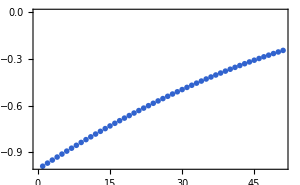

```mathematica
ListPlot[Table[%/.{De->1,A->100},{n,0,50}]]
```

```mathematica
Clear[norm,phiF];
phiF[n_,z_]:=phiF[n,z]=norm[n]*z^(A p[n])E^-z Hypergeometric1F1[-n,1+2A p[n],2z]
phiF[0,z]//ExpandAll
```

ⅇ^-z z^(-1/2+A √De) norm[0]

```mathematica
psi[n_,x_]:=psi[n,x]=phiF[n,z]/.z->A √De E^(-b x)
```

```mathematica
psi[0,x]//ExpandAll
```

(ⅇ^(-A √De ⅇ^(-b x)+b x) (A √De ⅇ^(-b x))^(1/2+A √De) norm[0])/(A √De)

```mathematica
Clear[norm];
Do[Module[{eq},
eq=Assuming[A √De>100,1==Integrate[phiF[i,z]^2/(b z),{z,0,Infinity}]//ExpandAll];
norm[i]=norm[i]/.Solve[eq,norm[i]][[1]]],{i,{0,1,2}}]
```

```mathematica
norm[#]&/@{0,1,2}
```

{-(2^(1/2 (-1+2 A √De)) √b)/(√Gamma[-1+2 A √De]),-(√(-4^(A √De) b+4^(A √De) A b √De))/(2 √Gamma[-3+2 A √De]),-(√(-45 2^(2+2 A √De) b+123 2^(2+2 A √De) A b √De-533 2^(2 A √De) A^2 b De+143 2^(1+2 A √De) A^3 b De^(3/2)-19 2^(2+2 A √De) A^4 b De^2+2^(3+2 A √De) A^5 b De^(5/2)))/(4 √Gamma[-2+2 A √De])}

```mathematica
psi[0,y/b]/√b/.{A->1,De->9}
```

-18 ⅇ^(-3 ⅇ^-y) (ⅇ^-y)^(5/2)

```mathematica
Floor[1/2+A √De]/.{A->1,De->9}
```

3

```mathematica
p/@Range[0,4]/.{A->1,De->9}
```

{5/2,3/2,1/2,-1/2,-3/2}

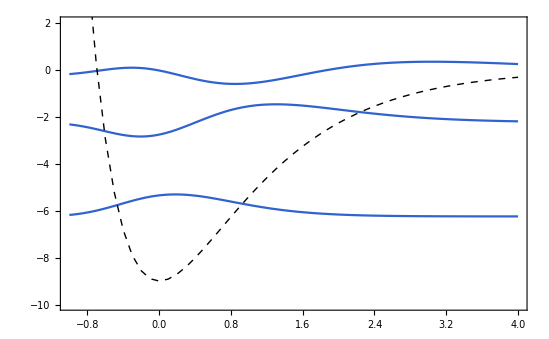

```mathematica
Plot[Table[e[n]-psi[n,y/b]/√b/.{A->1,De->9,b->1},{n,0,2}],{y,-1,4},PlotRange->{-10,2},
Epilog->{Dashed,
Line[Thread[{#,V/.{x->#/b}}/.{A->1,De->9}]&/@Range[-1,4,.1]]
}]
```

#### potential scattering

```mathematica
V=VHO E^(-b z^2);b=.1;
VHO=Vo+z^2/2;Vo=-2.0;
```

```mathematica
ksq[e_,z_]=2(e-V);
k[e_]=N[√(2e)];
```

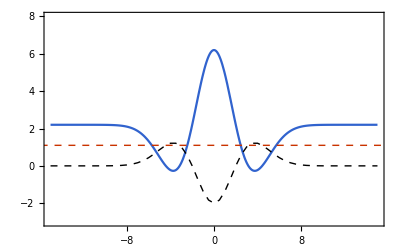

```mathematica
Plot[ksq[e,z]/.e->1.1,{z,-15,15},PlotRange->{-3,8},
Epilog->{Dashed,Red,
InfiniteLine[{0,1.1},{1,0}],
,{Dashed,Black,
Line[Thread[{#,V/.{e->1.1,z->#}}]&/@Range[-15,15,.5]]
}}]
```

```mathematica
Clear[psiNDSolve];
psiNDSolve[e_,opts___]:=psi[z]/.
NDSolve[
{psi''[z]+ksq[e,z]psi[z]==0,
psi[zo]==E^(I k[e]zo),
psi'[zo]==I k[e] E^(I k[e]zo)},
psi[z],{z,-zo,zo},opts][[1]]
```

here evaluate forces NDSolve to compute before construction of the Table begins.

```mathematica
Clear[dz];
psi0[e_,opts___]:=
Table[
Evaluate[{z,psiNDSolve[e,opts]}],
{z,-zo,zo-dz,dz}]
```

```mathematica
bkgrd[e_,zo_:15]:=Epilog->
{{Dashed,Line[{{-zo,e},{zo,e}}]},Line[Table[{z,V},{z,-zo,zo,.05}]]}
```

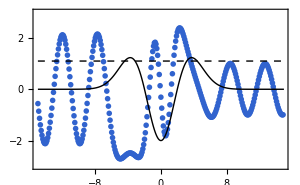

```mathematica
e=1.1;zo=15;dz=.1;
psi0e=psi0[e];
ListPlot[Re[psi0e],bkgrd[e],PlotRange->{-3,3}]
```

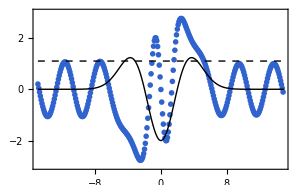

```mathematica
ListPlot[{#[[1]],Im@#[[2]]}&/@psi0e,bkgrd[e],PlotRange->{-3,3}]
```

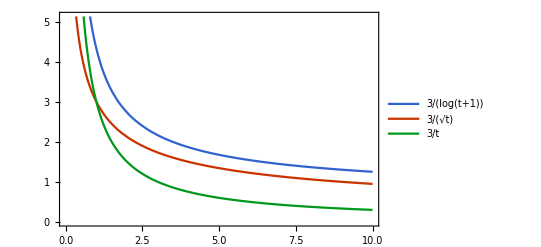

```mathematica
Plot[{3/Log[t+1],3/(√t),3/t},{t,0,10},PlotLegends->"Expressions"]
```

```mathematica
ha[V_]@psi_:=-h^2/(2m) D[psi,{z,2}]+V psi
```

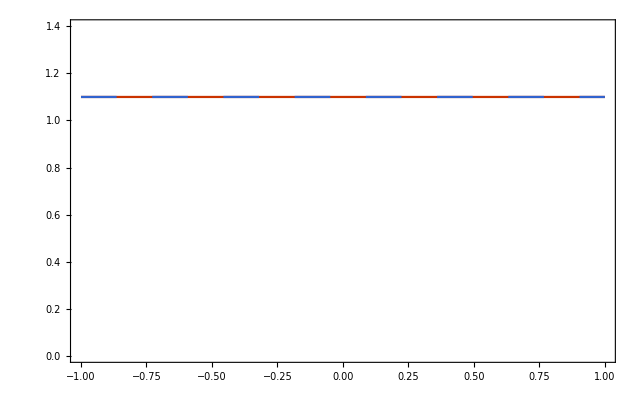

```mathematica
Module[{psiNDSolve},
psiNDSolve=First[psi/.
NDSolve[
{psi''[z]+ksq[e,z]psi[z]==0,
psi[zo]==E^(I k[e]zo),
psi'[zo]==I k[e] E^(I k[e]zo)},
psi,{z,-zo,zo}]];
Plot[{e,(-h^2/2/m*psiNDSolve''[z]+V psiNDSolve[z])/psiNDSolve[z]/.{h->1,m->1}//Re},{z,-1,1},PlotRange->{0,1.4},PlotStyle->{Red,Directive[Blue,Dashing[.04]]}]
]
```

```mathematica
fitIR[e_,psi_,nFit_:10]:=Fit[
Take[psi,nFit],
{E^(-I k[e]z),E^(I k[e]z)},z]
fitT[e_,psi_,nFit_:10]:=
Fit[
Take[psi,-nFit],
{E^(-I k[e]z),E^(I k[e]z)},z]
```

```mathematica
{fitIR[e,psi0e],fitT[e,psi0e]}//Chop
```

{(-5.8201×10^-8+0.953813 ⅈ) ⅇ^((0.-1.48324 ⅈ) z)+(1.06184-0.884458 ⅈ) ⅇ^((0.+1.48324 ⅈ) z),(-2.57814×10^-9-2.28828×10^-8 ⅈ) ⅇ^((0.-1.48324 ⅈ) z)+(1.+8.21402×10^-9 ⅈ) ⅇ^((0.+1.48324 ⅈ) z)}

```mathematica
fitIR[e,psi0e]
```

(-5.8201×10^-8+0.953813 ⅈ) ⅇ^((0.-1.48324 ⅈ) z)+(1.06184-0.884458 ⅈ) ⅇ^((0.+1.48324 ⅈ) z)

```mathematica
fitIR[e,psi0e]//FullSimplify
```

(1.06184+0.0693551 ⅈ) Cos[1.48324 z]+(1.83827+1.06184 ⅈ) Sin[1.48324 z]

```mathematica
aI[e_,psi_]:=fitIR[e,psi][[2,1]]
bR[e_,psi_]:=fitIR[e,psi][[1,1]]
R[e_,psi_]:=Abs[bR[e,psi]]^2
cT[e_,psi_]:=fitT[e,psi][[2,1]]
dR[e_,psi_]:=fitT[e,psi][[1,1]]
T[e_,psi_]:=Abs[cT[e,psi]]^2
```

```mathematica
psi[e_,psi0_,aI0_]:=Table[{psi0[[n,1]],psi0[[n,2]]/aI0},{n,Length[psi0]}]
```

```mathematica
psi[e_,psi0_,aI0_]:={#[[1]],#[[2]]/aI0}&/@psi0
```

```mathematica
{aI[e,psi0e],bR[e,psi0e],cT[e,psi0e],dR[e,psi0e]}
```

{1.06184-0.884458 ⅈ,-5.8201×10^-8+0.953813 ⅈ,1.+8.21402×10^-9 ⅈ,-2.57814×10^-9-2.28828×10^-8 ⅈ}

```mathematica
%/aI[e,psi0e]//Chop
```

{1.,-0.441735+0.530324 ⅈ,0.556004+0.463125 ⅈ,9.16414×10^-9-1.39169×10^-8 ⅈ}

```mathematica
psie=psi[e,psi0e,aI[e,psi0e]];
{aI[e,psie],bR[e,psie],cT[e,psie],dR[e,psie]}//Chop
```

{1.,-0.441735+0.530324 ⅈ,0.556004+0.463125 ⅈ,9.16414×10^-9-1.39169×10^-8 ⅈ}

```mathematica
e
```

1.1

```mathematica
{R[e,psie],T[e,psie],R[e,psie]+T[e,psie]}
```

{0.476374,0.523626,1.}

```mathematica
Repsi[e_,scale_,psi_]:=
{#[[1]],e+scale Re[#[[2]]]}&/@psi
Impsi[e_,scale_,psi_]:=
{#[[1]],e+scale Im[#[[2]]]}&/@psi
psisq[e_,scale_,psi_]:=
{#[[1]],e+scale Abs[#[[2]]]^2}&/@psi
```

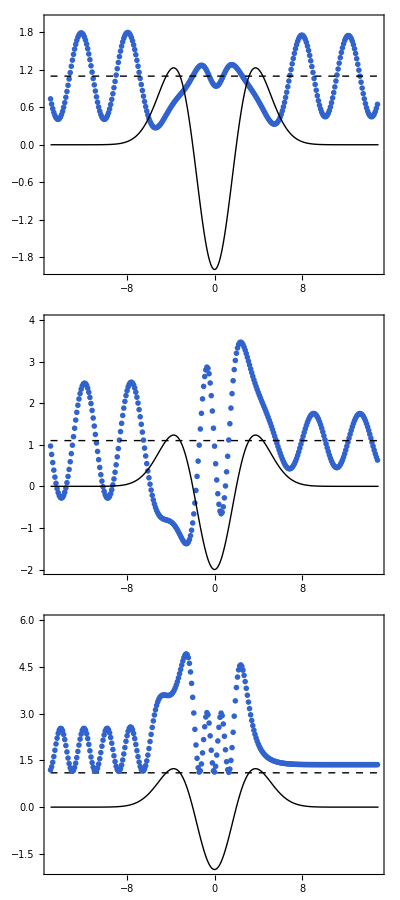

```mathematica
Column[{ListPlot[Repsi[e,.9,psie],bkgrd[e],PlotRange->{-2,2},ImageSize->Medium],
ListPlot[Impsi[e,.9,psie],bkgrd[e],PlotRange->{-2,4},ImageSize->Medium],
ListPlot[psisq[e,.5,psie],bkgrd[e],PlotRange->{-2,6},ImageSize->Medium]}]
```

resonance hunting

For barriers high and thick, the transmission is unlikely, except that the energy is just right, 100% transmission occurs when the incident and reflected waves to the left interfere destructively.

```mathematica
zo=15;dz=.1;
amplitudes=
Table[
Module[{psi0e,psie},
psi0e=psi0[e];
psie=psi[e,psi0e,aI[e,psi0e]];
{e,cT[e,psie],bR[e,psie]}],
{e,.47515,0.48445,.0003}];
```

```mathematica
Tvalues={#[[1]],Abs[#[[2]]]^2}&/@amplitudes;
```

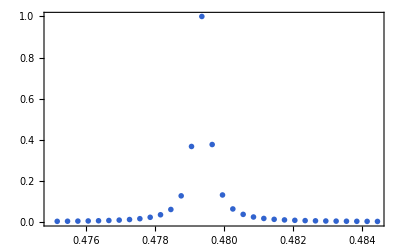

```mathematica
ListPlot[Tvalues,PlotRange->All]
```

```mathematica
amplitudes//{Abs[#[[15,1]]],Abs[#[[15,2]]]^2,Abs[#[[15,3]]]^2}&
```

{0.47935,0.999911,0.0000882829}

```mathematica
e=0.47935;zo=15;dz=.05;
psi0e=psi0[e];
psie=psi[e,psi0e,aI[e,psi0e]];
```

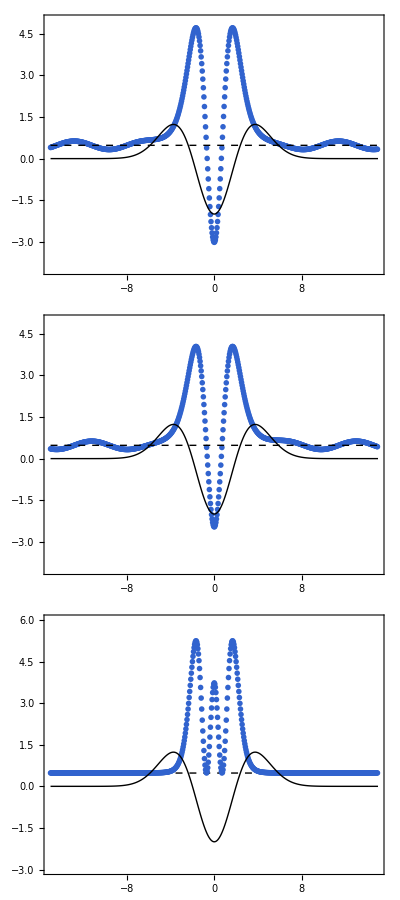

```mathematica
Column[{ListPlot[Repsi[e,.15,psie],bkgrd[e],PlotRange->{-4,5},ImageSize->Medium],
ListPlot[Impsi[e,.15,psie],bkgrd[e],PlotRange->{-4,5},ImageSize->Medium],
ListPlot[psisq[e,.0035,psie],bkgrd[e],PlotRange->{-3,6},ImageSize->Medium]}]
```

radial wavefunctions

via partial-wave analysis, 1D Schrodinger equation for the radial wavefunction is identical to psi[z], with r∈[0,Inf]

resonance parametrization

resonance energy er and FWHM g

```mathematica
Clear[e];
{cT[e_]=E^(I d)(I g/2)/(e-er+I g/2),bR[e_]=E^(I d)(e-er)/(e-er+I g/2)}
```

{(ⅈ ⅇ^(ⅈ d) g)/(2 (e-er+(ⅈ g)/2)),(ⅇ^(ⅈ d) (e-er))/(e-er+(ⅈ g)/2)}

```mathematica
bR[e]*bR[e]+cT[e]*cT[e]//ComplexExpand//Together
```

1

```mathematica
bR[e]*/bR[e]==-cT[e]*/cT[e]//ComplexExpand//FullSimplify
```

True

lorentzian (Breit-Wigner one-level formula)

```mathematica
T[e_]=cT[e]*cT[e]/.{((x_+I/2 y_)(x_-I/2 y_))^-1->(x^2+y^2/4)^-1}//ComplexExpand//FullSimplify
```

g^2/(4 (e-er)^2+g^2)

```mathematica
Solve[T[e]==1/2,e]//ExpandAll
```

{{e→er-g/2},{e→er+g/2}}

```mathematica
Im[cT[e]/cT[er]]/Re[cT[e]/cT[er]]//ComplexExpand//Together
```

(2 (e-er))/g

```mathematica
{er=amplitudes[[15,1]],cT[er]=amplitudes[[15,2]]}
```

{0.47935,0.16175+0.986787 ⅈ}

```mathematica
cTratio={#[[1]],Im[#[[2]]/cT[er]]/Re[#[[2]]/cT[er]]}&/@amplitudes;
```

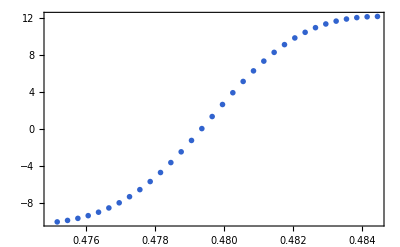

```mathematica
ListPlot[cTratio]
```

```mathematica
cTratioFit=Fit[Take[cTratio,{11,20}],{1,e},e]
```

-1988.96+4149.43 e

```mathematica
Solve[Collect[cTratioFit,e][[1]]==-2 erFit/gFit&&Collect[cTratioFit,e][[2]]==2 e/gFit,{erFit,gFit}]//N
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{erFit→0.479333,gFit→0.000481993}}

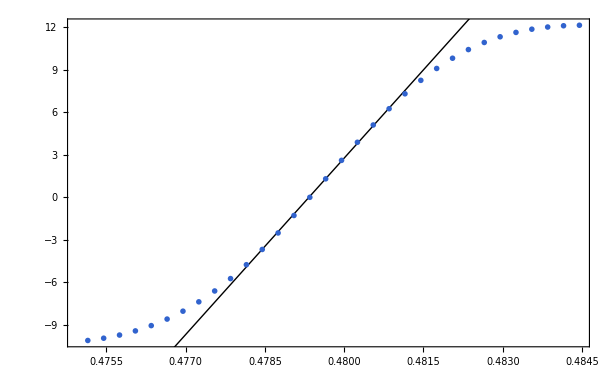

```mathematica
ListPlot[cTratio,
Epilog->InfiniteLine[Table[{e,(2 (e-erFit))/gFit/.{erFit->0.4793331967506907,gFit->0.0004819934952958183}},{e,{1,10}}]]]
```

wave packet impact

construct a time-dependent scattering wave packet as a linear superposition of continuum eigenfunctions belonging to a small range of eigenenergies with an average value eP.

consider a free-particle wave packet, the time-dependent superposition of planewaves

```mathematica
freePacket[t_,dz_:1.0,zP_:-50]:=
Table[Evaluate[
{z,Sum[f[e] E^(-I e t)E^(I k[e](z-zP)),{e,emin,emax,de}]}
],{z,-zo,zo,dz}]
```

```mathematica
{eP=1.13,emin=1.01,emax=1.25,de=.04};
```

```mathematica
{f[e_]=E^(-(e-eP)^2/2/w)/nrm,w=.005,nrm=1.76653};
```

```mathematica
Sum[f[e]^2,{e,emin,emax,de}]
```

1.

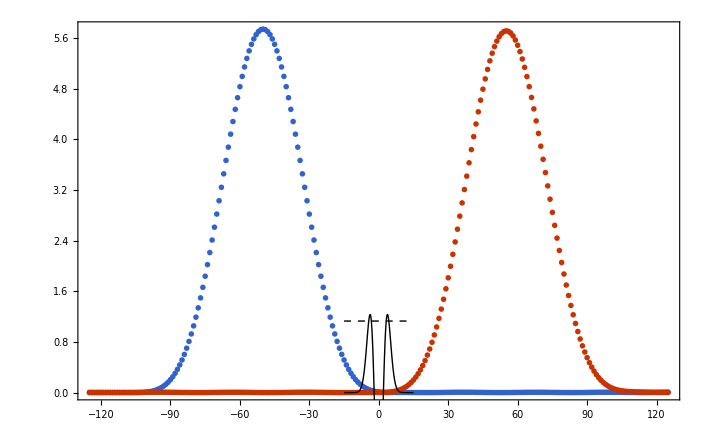

```mathematica
Module[{freePacket,zo=125},
freePacket[t_,dz_:1.0,zP_:-50]:=
Table[Evaluate[
{z,Sum[f[e] E^(-I e t)E^(I k[e](z-zP)),{e,emin,emax,de}]}
],{z,-zo,zo,dz}];
ListPlot[{{#[[1]],Abs[#[[2]]]^2}&/@freePacket[0],{#[[1]],Abs[#[[2]]]^2}&/@freePacket[70]},PlotRange->All,bkgrd[eP]]]
```

```mathematica
psiPacket[t_,zP_:-50]:=
Table[
{psi[eP][[n,1]],
Sum[
f[e] E^(-I e t)E^(-I k[e]zP)psi[e][[n,2]],{e,emin,emax,de}]},{n,Length[psi[eP]]}]
```

```mathematica
zo=30;dz=.1;
Do[
Module[{psi0e},
psi0e=psi0[e,MaxSteps->1500];
psi[e]=psi[e,psi0e,aI[e,psi0e]];
],{e,emin,emax,de}]
```

```mathematica
psiPlot[t_]:=
ListLinePlot[
Evaluate[psisq[eP,0.65,psiPacket[t]]],
bkgrd[eP],PlotRange->{-3,15}];
freePlot[t_]:=
ListLinePlot[
Evaluate[psisq[eP,.65,freePacket[t]]],bkgrd[eP],PlotRange->{-3,15}];
psifreePlot[t_]:=
Show[
psiPlot[t],freePlot[t]];
```

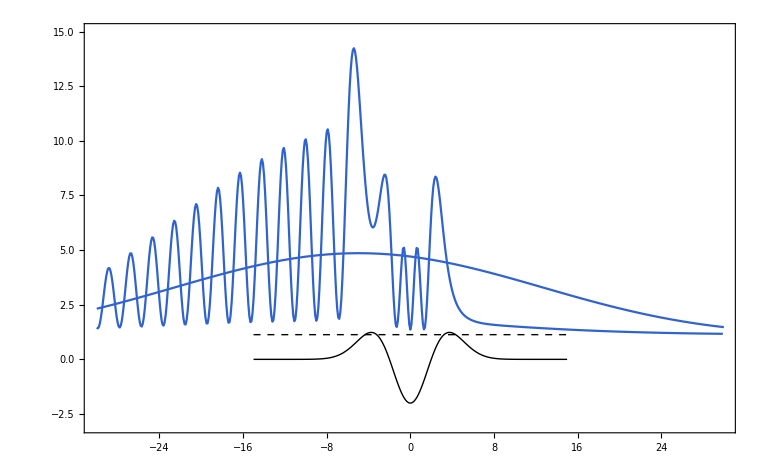

```mathematica
Show[psifreePlot[30],DisplayFunction->$DisplayFunction]
```

```mathematica
Manipulate[Show[psifreePlot[t],DisplayFunction->$DisplayFunction],{t,0,120,5}]
```

note the resonance lifetime,